## Analytical Solution

```mathematica
ClearAll["Global`*"];
```

## Problem Setup "Run Section"

```mathematica
R0 = 1; 
R1 = 2; 
τ = 0.05; 
facBC = 1; 

χτ=0.33392;
χh=0.444065;

g1value=Sqrt[2/Pi];
g2value=-(Sqrt[2(1-χτ)] Sqrt[χτ χh]-6 χτ χh)/(3 Sqrt[5 Pi] χτ χh);
g3value=-(Sqrt[2] (χτ-1-18 χτ χh+3 Sqrt[2] (2-9 χh) Sqrt[χτ χh (1-χτ)]))/(45 Sqrt[Pi] χτ χh);
g4value=2 Sqrt[2/Pi];
g5value=-(Sqrt[2] Sqrt[2-3 χh] Sqrt[χh χτ]-8 χh χτ)/(5 Sqrt[Pi] χh χτ);
g6value=-(Sqrt[2] (-2+χh (3-32 χτ))+(16-75 χτ) Sqrt[2-3 χh] Sqrt[χh χτ])/(50 Sqrt[Pi] χh χτ);

(*g1value = Sqrt[2/π]; 
g2value = 0; 
g3value =0; 
g4value = 2 Sqrt[2/π]; 
g5value = 0; 
g6value = 0; 
g1value = g1; 
g2value = g2; 
g3value = g3; 
g4value = g4; 
g5value = g5; 
g6value = g6; *)

v0 = 2.; 
vR = -1.; 
p0 = 0.; 
eps = 10^(-5); 
temperature0 = 1.; 
temperature1 = 2.; 

g1BC[r_, theta_] = Piecewise[{
                            {g1value, r == R0}, {g1value, r == R1}}]; 

g2BC[r_, theta_] = Piecewise[{
                            {g2value, r == R0}, {g2value, r == R1}}]; 
g3BC[r_, theta_] = Piecewise[{
                            {g3value, r == R0}, {g3value, r == R1}}]; 
g4BC[r_, theta_] = Piecewise[{
                            {g4value, r == R0}, {g4value, r == R1}}]; 
g5BC[r_, theta_] = Piecewise[{
                            {g5value, r == R0}, {g5value, r == R1}}]; 
g6BC[r_, theta_] = Piecewise[{
                            {g6value, r == R0}, {g6value, r == R1}}]; 


temperatureBC[r_, theta_] = Piecewise[{
                            {temperature0, r == R0}, {temperature1, r == R1}}]; 
vtBC[r_, theta_] = Piecewise[{
                            {vR, r == R0}, {(-v0)*Sin[theta], r == R1}}]; 
vnBC[r_, theta_] = Piecewise[{
                            {0, r == R0}, {v0*Cos[theta], r == R1}}]; 
pBC[r_, theta_] = Piecewise[{
                            {0, r == R0}, {p0*Cos[theta], r == R1}}]; 
epspBC[r_, theta_] = Piecewise[{
                            {1, r == R0}, {1, r == R1}}]; 
epsvBC[r_, theta_] = Piecewise[{
                            {eps, r == R0}, {1, r == R1}}]; 

nn[R0] = -1; 
nn[R1] = 1; 
tt[R0] = -1; 
tt[R1] = 1; 
setup[r_, theta_] := {
  g1 -> g1BC[r, theta],
g2 -> g2BC[r, theta],
g3 -> g3BC[r, theta],
g4 -> g4BC[r, theta],
g5 -> g5BC[r, theta],
g6 -> g6BC[r, theta],
  temperatureW -> temperatureBC[r, theta], 
  vnW -> vnBC[r, theta], 
  vtW -> vtBC[r, theta], 
  pW -> pBC[r, theta], 
  epsp -> epspBC[r, theta], 
  epsv -> epsvBC[r, theta]}
```

```mathematica
(* analytical solution display *)
style=Dashing[0.01];
theory = theory1 = "E13";
```

```mathematica
g1value*1.0
g2value*1.0
g3value*1.0
g4value*1.0
g5value*1.0
g6value*1.0
```

0.797885

0.252538

0.717125

1.59577

0.564054

0.799082

## Cylindrical Differential Operator "Run Section"

```mathematica
$Assumptions = {r > 0, 0 < theta < Pi, Element[{theta, r, z}, Reals]}; 
xx = {r, theta, z}; 
P = {r*Cos[theta], r*Sin[theta], z}; 
J = Simplify[Table[D[P[[nu]], xx[[mu]]], {nu, 1, 3}, {mu, 1, 3}]]; 
Ji = Simplify[Inverse[J]]; 
(* metric coefficients *)
gg = Simplify[Transpose[J] . J]; 
gi = Simplify[Inverse[gg]]; 
(* Christoffel symbols*)
Gam = Simplify[Table[(1/2)*Sum[gi[[lambda,sigma]]*(D[gg[[sigma,nu]], xx[[mu]]] + 
         D[gg[[mu,sigma]], xx[[nu]]] - D[gg[[mu,nu]], xx[[sigma]]]), 
       {sigma, 1, 3}], {lambda, 1, 3}, {mu, 1, 3}, {nu, 1, 3}]]; 
       
(* gradient, Laplace of scalars *)
Grad0[S_] := (temp = Simplify[Table[D[S, xx[[i]]], {i, 1, 3}]]; 
   Simplify[Table[Sqrt[gi[[i,i]]]*temp[[i]], {i, 1, 3}]])
   
Laplace0[S_] := (temp1 = Simplify[Table[D[S, xx[[i]]], {i, 1, 3}]]; 
   temp2 = Simplify[Table[D[temp1[[i]], xx[[k]]] - Sum[Gam[[sigma,i,k]]*temp1[[sigma]], 
        {sigma, 1, 3}], {i, 1, 3}, {k, 1, 3}]]; 
   Simplify[Sum[gi[[k,k]]*temp2[[k,k]], {k, 1, 3}]])
   
(* gradient, divergence, Laplace of vectors *)
Grad1[V_] := (temp = Simplify[Table[V[[i]]/Sqrt[gg[[i,i]]], {i, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i]], xx[[k]]] + Sum[Gam[[i,sigma,k]]*temp[[sigma]], 
        {sigma, 1, 3}], {i, 1, 3}, {k, 1, 3}]]; 
   Simplify[Table[Sqrt[gg[[i,i]]]*Sqrt[gi[[k,k]]]*temp1[[i,k]], {i, 1, 3}, 
     {k, 1, 3}]])

Div1[V_] := (temp = Simplify[Table[V[[i]]/Sqrt[gg[[i,i]]], {i, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i]], xx[[k]]] + Sum[Gam[[i,sigma,k]]*temp[[sigma]], 
        {sigma, 1, 3}], {i, 1, 3}, {k, 1, 3}]]; Simplify[Sum[temp1[[k,k]], {k, 1, 3}]])

Laplace1[V_] := (temp = Simplify[Table[V[[i]]/Sqrt[gg[[i,i]]], {i, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i]], xx[[k]]] + Sum[Gam[[i,sigma,k]]*temp[[sigma]], 
        {sigma, 1, 3}], {i, 1, 3}, {k, 1, 3}]]; 
   temp2 = Simplify[Table[D[temp1[[i,j]], xx[[k]]] + Sum[Gam[[i,sigma,k]]*temp1[[sigma,j]], 
        {sigma, 1, 3}] - Sum[Gam[[sigma,j,k]]*temp1[[i,sigma]], {sigma, 1, 3}], {i, 1, 3}, 
      {j, 1, 3}, {k, 1, 3}]]; 
   Simplify[Table[Sqrt[gg[[i,i]]]*Sum[gi[[k,k]]*temp2[[i,k,k]], {k, 1, 3}], 
     {i, 1, 3}]])
     
(* gradient, divergence, Laplace of matrices *)
Div2[V_] := (temp = Simplify[Table[V[[i,j]]/Sqrt[gg[[i,i]]*gg[[j,j]]], {i, 1, 3}, 
      {j, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i,j]], xx[[k]]] + 
       Sum[Gam[[i,sigma,k]]*temp[[sigma,j]], {sigma, 1, 3}] + Sum[Gam[[j,sigma,k]]*temp[[i,sigma]], 
        {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, {k, 1, 3}]]; 
   Simplify[Table[Sqrt[gg[[i,i]]]*Sum[temp1[[i,k,k]], {k, 1, 3}], {i, 1, 3}]])

Grad2[V_] := (temp = Simplify[Table[V[[i,j]]/Sqrt[gg[[i,i]]*gg[[j,j]]], {i, 1, 3}, 
      {j, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i,j]], xx[[k]]] + 
       Sum[Gam[[i,sigma,k]]*temp[[sigma,j]], {sigma, 1, 3}] + Sum[Gam[[j,sigma,k]]*temp[[i,sigma]], 
        {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, {k, 1, 3}]]; 
   Simplify[Table[Sqrt[gg[[i,i]]]*Sqrt[gg[[j,j]]]*Sqrt[gi[[k,k]]]*temp1[[i,j,k]], 
     {i, 1, 3}, {j, 1, 3}, {k, 1, 3}]])

Laplace2[V_] := (temp = Simplify[Table[V[[i,j]]/Sqrt[gg[[i,i]]*gg[[j,j]]], 
      {i, 1, 3}, {j, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i,j]], xx[[k]]] + Sum[Gam[[i,sigma,k]]*temp[[sigma,j]], 
        {sigma, 1, 3}] + Sum[Gam[[j,sigma,k]]*temp[[i,sigma]], {sigma, 1, 3}], {i, 1, 3}, 
      {j, 1, 3}, {k, 1, 3}]]; 
   temp2 = Simplify[Table[D[temp1[[i,j,k]], xx[[l]]] + 
       Sum[Gam[[i,sigma,l]]*temp1[[sigma,j,k]], {sigma, 1, 3}] + 
       Sum[Gam[[j,sigma,l]]*temp1[[i,sigma,k]], {sigma, 1, 3}] - 
       Sum[Gam[[sigma,k,l]]*temp1[[i,j,sigma]], {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, 
      {k, 1, 3}, {l, 1, 3}]]; 
   Simplify[Table[Sqrt[gg[[i,i]]]*Sqrt[gg[[j,j]]]*
      Sum[gi[[k,k]]*temp2[[i,j,k,k]], {k, 1, 3}], {i, 1, 3}, {j, 1, 3}]])

(* gradient, divergence, Laplace of 3-tensors *) 
Div3[V_] := (temp = Simplify[Table[V[[i,j,k]]/Sqrt[gg[[i,i]]*gg[[j,j]]*gg[[k,k]]], 
      {i, 1, 3}, {j, 1, 3}, {k, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i,j,k]], xx[[l]]] + 
       Sum[Gam[[i,sigma,l]]*temp[[sigma,j,k]], {sigma, 1, 3}] + 
       Sum[Gam[[j,sigma,l]]*temp[[i,sigma,k]], {sigma, 1, 3}] + 
       Sum[Gam[[k,sigma,l]]*temp[[i,j,sigma]], {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, 
      {k, 1, 3}, {l, 1, 3}]]; Simplify[Table[Sqrt[gg[[i,i]]*gg[[j,j]]]*
      Sum[temp1[[i,j,k,k]], {k, 1, 3}], {i, 1, 3}, {j, 1, 3}]])
      
Grad3[V_] := (temp = Simplify[Table[V[[i,j,k]]/Sqrt[gg[[i,i]]*gg[[j,j]]*gg[[k,k]]], 
      {i, 1, 3}, {j, 1, 3}, {k, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i,j,k]], xx[[l]]] + 
       Sum[Gam[[i,sigma,l]]*temp[[sigma,j,k]], {sigma, 1, 3}] + 
       Sum[Gam[[j,sigma,l]]*temp[[i,sigma,k]], {sigma, 1, 3}] + 
       Sum[Gam[[k,sigma,l]]*temp[[i,j,sigma]], {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, 
      {k, 1, 3}, {l, 1, 3}]]; Simplify[Table[Sqrt[gg[[i,i]]]*Sqrt[gg[[j,j]]]*
      Sqrt[gg[[k,k]]]*Sqrt[gi[[l,l]]]*temp1[[i,j,k,l]], {i, 1, 3}, {j, 1, 3}, 
     {k, 1, 3}, {l, 1, 3}]])
     
Laplace3[V_] := 
  (temp = Simplify[Table[V[[i,j,k]]/Sqrt[gg[[i,i]]*gg[[j,j]]*gg[[k,k]]], {i, 1, 3}, 
      {j, 1, 3}, {k, 1, 3}]]; 
   temp1 = Simplify[Table[D[temp[[i,j,k]], xx[[l]]] + 
       Sum[Gam[[i,sigma,l]]*temp[[sigma,j,k]], {sigma, 1, 3}] + 
       Sum[Gam[[j,sigma,l]]*temp[[i,sigma,k]], {sigma, 1, 3}] + 
       Sum[Gam[[k,sigma,l]]*temp[[i,j,sigma]], {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, 
      {k, 1, 3}, {l, 1, 3}]]; 
   temp2 = Simplify[Table[D[temp1[[i,j,k,l]], xx[[m]]] + 
       Sum[Gam[[i,sigma,m]]*temp1[[sigma,j,k,l]], {sigma, 1, 3}] + 
       Sum[Gam[[j,sigma,m]]*temp1[[i,sigma,k,l]], {sigma, 1, 3}] + 
       Sum[Gam[[k,sigma,m]]*temp1[[i,j,sigma,l]], {sigma, 1, 3}] - 
       Sum[Gam[[sigma,l,m]]*temp1[[i,j,k,sigma]], {sigma, 1, 3}], {i, 1, 3}, {j, 1, 3}, 
      {k, 1, 3}, {l, 1, 3}, {m, 1, 3}]]; 
   Simplify[Table[Sqrt[gg[[i,i]]]*Sqrt[gg[[j,j]]]*Sqrt[gg[[k,k]]]*
      Sum[gi[[l,l]]*temp2[[i,j,k,l,l]], {l, 1, 3}], {i, 1, 3}, {j, 1, 3}, 
     {k, 1, 3}]])
```

## Solution Ansatz "Run Section"

```mathematica
coef[expr_, var_, idx_] := Flatten[Normal[CoefficientArrays[Extract[expr, idx], 
      var]]]; 
TraceFreeSym2[mat_] := Block[{perm, sym1, trace}, perm = Permutations[{1, 2}]; 
    sym1 = Expand[(1/Length[perm])*Sum[Transpose[mat, idx], {idx, perm}]]; 
    trace = Sum[sym1[[jj,jj]], {jj, 1, 3}]; 
    Expand[sym1 - (1/3)*trace*Table[KroneckerDelta[ii, jj], {ii, 1, 3}, {jj, 1, 3}]]]
TraceFreeSym3[mat_] := Block[{perm, sym1, trace}, perm = Permutations[{1, 2, 3}]; 
    sym1 = Expand[(1/Length[perm])*Sum[Transpose[mat, idx], {idx, perm}]]; 
    trace = Sum[sym1[[All,jj,jj]], {jj, 1, 3}]; 
    Expand[sym1 - (1/5)*Table[trace[[ii]]*KroneckerDelta[jj, kk] + 
         trace[[jj]]*KroneckerDelta[ii, kk] + trace[[kk]]*KroneckerDelta[ii, jj], 
        {ii, 1, 3}, {jj, 1, 3}, {kk, 1, 3}]]]
scalarIdx = {{}}; 
vectorIdx = {{1}, {2}}; 
tensor2Idx = {{1, 1}, {1, 2}, {2, 2}}; 
tensor3Idx = {{1, 1, 1}, {1, 1, 2}, {1, 2, 2}, {2, 2, 2}}; 

Clear[Kn, a, b, alpha, beta, c, d, gamma, kappa, omega, a0, b0, c0, d0, alpha0, beta0, gamma0, omega0, kappa0, 
  BK, BI, lambda, lambdaList]
nVar = 18; 
ansatz = {a, b, alpha, beta, c, d, gamma, kappa, omega, a0, b0, c0, d0, alpha0, beta0, gamma0, omega0, kappa0}; 

temperature[r_, theta_] = c0[r] + c[r]*Cos[theta]; 

hr[r_, theta_] = alpha0[r] + Cos[theta]*alpha[r]; 
hTheta[r_, theta_] = beta0[r] - Sin[theta]*beta[r]; 
h[r_, theta_] = {hr[r, theta], hTheta[r, theta], 0}; 

vr[r_, theta_] = a0[r] + Cos[theta]*a[r]; 
vTheta[r_, theta_] = b0[r] - Sin[theta]*b[r]; 
v[r_, theta_] = {vr[r, theta], vTheta[r, theta], 0}; 

p[r_, theta_] = d0[r] + d[r]*Cos[theta]; 

rho[r_, theta_] = p[r, theta] - temperature[r, theta]; 

ℼrr[r_, theta_] = Cos[theta]*gamma[r] + gamma0[r]; 
ℼThetaTheta[r_, theta_] = -(Cos[theta]*omega[r] + omega0[r]); 
ℼrTheta[r_, theta_] = kappa0[r] + Sin[theta]*kappa[r]; 
ℼzz[r_, theta_] = -ℼrr[r, theta] - ℼThetaTheta[r, theta]; 
ℼ[r_, theta_] = {{ℼrr[r, theta], ℼrTheta[r, theta], 0}, {ℼrTheta[r, theta], ℼThetaTheta[r, theta], 0}, 
    {0, 0, ℼzz[r, theta]}};
```

## Define Equations "Run Section"

```mathematica
βv1=.;
βv2=.;
βθ2=.;
βθ3=.;
βτ2=.;

ω2=.;
ω3=.;
θ2=.;
θ4=.;
μ=.;
κ=.;
```

```mathematica
(*Maxwell Molecules*)
ω2=2;
ω3=3;
θ2=45/8;
θ4=3;
μ=1;
κ=15/4;



βv1=χτ ω2-2 μ;
βv2=χτ Sqrt[ω2];
βθ2=χh θ2-κ;
βθ3=χh Sqrt[θ2];
βτ2=(ω3+θ4)/(2 Sqrt[ω2 θ2]);
```

```mathematica
dv[r_, theta_]=Kn TraceFreeSym2[Grad1[v[r, theta]]];
dvRR[r_,theta_]=Kn TraceFreeSym2[Grad1[v[r,theta]]][[1,1]];
dvRTheta[r_,theta_]=Kn TraceFreeSym2[Grad1[v[r,theta]]][[1,2]];
dθ[r_, theta_]=Kn Grad0[temperature[r, theta]]; 
dθR[r_,theta_]=Kn Grad0[temperature[r,theta]][[1]];
dθTheta[r_,theta_]=Kn Grad0[temperature[r,theta]][[2]];
(* E13 equations *)

eqns0 = {
   Div1[v[r, theta]],
   Grad0[p[r, theta]] +βv1 Div2[dv[r,theta]]+βv2 Div2[ℼ[r, theta]],
   Div1[v[r, theta]]+βθ2 Div1[dθ[r,theta]]+βθ3 Div1[h[r, theta]],
   βv2 TraceFreeSym2[Grad1[v[r, theta]]]+βτ2 TraceFreeSym2[Grad1[h[r, theta]]]+χτ (1/Kn)*ℼ[r, theta],
   βθ3 Grad0[temperature[r, theta]] +βτ2 Div2[ℼ[r, theta]]+χh(1/Kn)*h[r, theta]
   };
```

```mathematica
(* E13 boundary conditions *)

 BCeqn0 = { 
   (-epsp)*(vn - vnW) + epsv*(rho + temperature + facBC*(βv1  dvnn+βv2 ℼnn) + pW), 
-(βv1  dvnt+βv2 ℼnt) + g1*(vt - vtW) + g2*ht,
   -βτ2 ℼnt + g2*(vt - vtW) + g3*ht, 
 -(βθ2 dθn+βθ3 hn) + g4*(temperature - temperatureW) +g5* ℼnn, 
   -βτ2 hn + g5*(temperature - temperatureW) +g6* ℼnn

   };

{BCrhs,BC}=Normal[CoefficientArrays[BCeqn0,{rho,vn,vt,dvnn,dvnt,temperature,dθn,dθt,ℼnn,ℼnt,ℼtt,hn,ht}   (*these two now present in BCeqn0*)]];
```

## Solve Equations by Ansatz "Run Section"

```mathematica
eqns = {coef[eqns0[[1]], {Cos[theta], Sin[theta]}, scalarIdx], 
   coef[eqns0[[2]], {Cos[theta], Sin[theta]}, vectorIdx],
   coef[eqns0[[3]], {Cos[theta], Sin[theta]}, scalarIdx ], 
   coef[eqns0[[4]], {Cos[theta], Sin[theta]}, tensor2Idx],
   coef[eqns0[[5]], {Cos[theta], Sin[theta]}, vectorIdx]
   };
```

```mathematica
Print["Computing eigenvalues of solution modes."]
Clear[lambda]
eqnsL = eqns /. Power[r, n_?Negative] -> 0;
{a[r_], b[r_], alpha[r_], beta[r_], c[r_], d[r_], gamma[r_], kappa[r_], omega[r_], a0[r_], b0[r_], 
    c0[r_], d0[r_], alpha0[r_], beta0[r_], gamma0[r_], omega0[r_], kappa0[r_]} = 
   Table[v$[j]*Exp[lambda*r], {j, 1, nVar}]; 
coefs = Table[v$[j], {j, 1, nVar}]; 
eqnsL1 = Select[Flatten[Expand[Exp[(-lambda)*r]*eqnsL /. Kn -> 1]], Length[#1] > 0 & ];
vars2 = Sort[DeleteDuplicates[(Extract[eqnsL1, Append[#1, -1]] & ) /@ 
      Position[eqnsL1, (val_)*lambda^2*v$[_]]]];
eqnsL2 = Join[eqnsL1 /. Thread[Expand[lambda^2*vars2] -> lambda*w /@ Range[Length[vars2]]], 
    w /@ Range[Length[vars2]] - Expand[lambda*vars2]];
lambdaList = Select[DeleteDuplicates[
     lambda /. Solve[Det[CoefficientArrays[eqnsL2, Join[coefs, 
            w /@ Range[Length[vars2]]]][[2]]] == 0, lambda]],N[#] > 0 & ]

(*lambdaList=DeleteDuplicates[lambda/. Solve[Det[CoefficientArrays[eqnsL2,Join[coefs,w/@Range[Length[vars2]]]][[2]]]==0,lambda]]
Then use all of them—real and complex*)
 (*safe for complex numbers*)
```

Computing eigenvalues of solution modes.

{0.746021,0.912505}

```mathematica
Print["Computing bulk solution."]
kmax = 5; 
phi = Flatten[Join[{1, Log[r]}, Table[{r^k, r^(-k)}, {k, 1, kmax}]]]; 
{a[r_], b[r_], alpha[r_], beta[r_], c[r_], d[r_], gamma[r_], kappa[r_], omega[r_], a0[r_], b0[r_], 
    c0[r_], d0[r_], alpha0[r_], beta0[r_], gamma0[r_], omega0[r_], kappa0[r_]} = 
   Table[Table[v$[j, k], {k, 1, Length[phi]}] . phi, {j, 1, nVar}]; 
coefs = Flatten[Table[Table[v$[j, k], {k, 1, Length[phi]}], {j, 1, nVar}]]; 
{bb, AA} = Normal[CoefficientArrays[Expand[Flatten[eqns /. {Kn -> 1}]] /. 
        {Log[r] -> Logr[0]} /. {r^(j_.) -> rr[j]} /. {Logr[0]*rr[k_] -> Logr[k]}, 
     Join[Table[rr[k], {k, -2*kmax, 2*kmax}], Table[Logr[k], 
       {k, -2*kmax, 2*kmax}]]]]; 
{bb, AA} = Normal[CoefficientArrays[Select[Flatten[{bb, AA}], Length[#1] > 0 & ], 
     coefs]]; 
nspc = NullSpace[AA]; 
nC = Length[nspc]; 
sol0 = Sum[C[i]*Table[Table[v$[j, k], {k, 1, Length[phi]}] . phi, {j, 1, nVar}] /. 
     Thread[coefs -> nspc[[i]]], {i, 1, nC}];
```

Computing bulk solution.

```mathematica
TableForm[%]
```

C[3] (0.202286+(3.46945×10^-18)/r^5+(2.46331×10^-16)/r^4-(3.19189×10^-16)/r^3-0.213115/r^2+(6.93889×10^-18)/r+5.75928×10^-16 r+0.0547108 r^2-7.28584×10^-17 r^3+8.41341×10^-17 r^4-5.72459×10^-17 r^5-0.191633 Log[r])+C[2] (0.0426675+(3.14419×10^-17)/r^5-(9.54098×10^-18)/r^4-(6.83047×10^-16)/r^3-0.329054/r^2+(1.52656×10^-16)/r-1.02349×10^-16 r-0.0675401 r^2-2.04697×10^-16 r^3-9.30245×10^-17 r^4+1.17961×10^-16 r^5-0.110892 Log[r])+C[11] (-0.287872+(2.94903×10^-17)/r^5+(2.498×10^-16)/r^4+(4.35416×10^-16)/r^3+0.0330988/r^2+(2.91434×10^-16)/r+1.11022×10^-16 r+0.013329 r^2+1.38778×10^-16 r^3+1.71738×10^-16 r^4-7.11237×10^-17 r^5-0.0387141 Log[r])+C[6] (-0.0390057+(8.67362×10^-19)/r^5+(1.99493×10^-17)/r^4-(1.26418×10^-16)/r^3+0.00181968/r^2-(9.97466×10^-17)/r-1.04083×10^-17 r-0.000969858 r^2-2.08167×10^-17 r^3-9.28077×10^-17 r^4-8.67362×10^-18 r^5-0.00389417 Log[r])+C[9] (0.0016337-(1.49078×10^-19)/r^5-(2.49366×10^-18)/r^4-(1.83095×10^-17)/r^3-0.00154136/r^2-(2.43945×10^-17)/r-2.76472×10^-18 r+0.00203397 r^2-1.12215×10^-17 r^3+1.21566×10^-17 r^4+8.67362×10^-19 r^5-0.0037152 Log[r])+C[7] (0.0323077-(6.50521×10^-19)/r^5-(2.25514×10^-17)/r^4+(4.6187×10^-17)/r^3-0.0143353/r^2+(1.79544×10^-16)/r-2.22912×10^-16 r-0.00129648 r^2-3.90313×10^-18 r^3+9.32414×10^-18 r^4+1.47451×10^-17 r^5-0.00108741 Log[r])+C[8] (0.00603205+(2.43945×10^-18)/r^5+(1.81062×10^-17)/r^4+(4.58346×10^-17)/r^3+0.000836564/r^2+(3.70797×10^-17)/r-9.97466×10^-18 r+0.000849891 r^2+1.73472×10^-18 r^3-4.14707×10^-18 r^4+4.17418×10^-18 r^5+0.000433475 Log[r])+C[10] (0.0001672+(2.10064×10^-19)/r^5-(2.23956×10^-17)/r^4+(4.93702×10^-17)/r^3-0.0125563/r^2-(3.02492×10^-17)/r-1.89735×10^-19 r-0.00171271 r^2-3.12013×10^-17 r^3+2.01043×10^-17 r^4-2.07354×10^-17 r^5+0.00567426 Log[r])+C[5] (0.134458+(2.60209×10^-18)/r^5-(1.73472×10^-17)/r^4+(1.83881×10^-16)/r^3+0.00531299/r^2-(3.1225×10^-17)/r+2.42861×10^-17 r-0.00188254 r^2+6.93889×10^-18 r^3-1.38778×10^-17 r^4+1.56125×10^-17 r^5+0.00590693 Log[r])+C[4] (-0.105852-(1.73472×10^-18)/r^5+(5.37764×10^-17)/r^4+(2.94903×10^-17)/r^3-0.0436798/r^2+(3.60822×10^-16)/r-8.67362×10^-17 r-0.00830831 r^2-2.68882×10^-16 r^3-3.31766×10^-16 r^4+2.15106×10^-16 r^5+0.0540796 Log[r])+C[1] (0.54963-(1.38778×10^-17)/r^5+(5.30825×10^-16)/r^3-0.0917324/r^2+(4.57967×10^-16)/r+9.71445×10^-17 r+0.0017144 r^2-2.77556×10^-16 r^3+1.83881×10^-16 r^4-1.38778×10^-17 r^5+0.0643178 Log[r])+C[12] (-0.247777+(9.02056×10^-17)/r^5-(9.71445×10^-17)/r^4+(5.3256×10^-16)/r^3-0.470242/r^2+(6.17562×10^-16)/r-6.93889×10^-18 r+0.023897 r^2-2.81025×10^-16 r^3+2.87964×10^-16 r^4-1.76942×10^-16 r^5+0.162055 Log[r])
C[3] (0.0106528+(8.32667×10^-17)/r^5+(3.29597×10^-17)/r^4+(9.71445×10^-17)/r^3+0.213115/r^2+(5.26489×10^-16)/r+4.38885×10^-16 r+0.164132 r^2-2.06432×10^-16 r^3-5.51642×10^-16 r^4-2.25514×10^-17 r^5-0.191633 Log[r])+C[2] (-0.0682247-(1.5786×10^-16)/r^5+(1.03433×10^-16)/r^4+(3.05311×10^-16)/r^3+0.329054/r^2+(6.61363×10^-16)/r-5.96962×10^-16 r-0.20262 r^2-1.36609×10^-16 r^3+9.83588×10^-16 r^4+1.80411×10^-16 r^5-0.110892 Log[r])+C[11] (-0.326586+(6.245×10^-17)/r^5-(2.34188×10^-17)/r^4-(2.98372×10^-16)/r^3-0.0330988/r^2+(5.79398×10^-16)/r+1.8735×10^-16 r+0.0399869 r^2+2.34188×10^-16 r^3+2.77556×10^-17 r^4-9.71445×10^-17 r^5-0.0387141 Log[r])+C[6] (-0.0428999+(6.93889×10^-18)/r^5+(2.81893×10^-18)/r^4+(6.59195×10^-17)/r^3-0.00181968/r^2-(1.82146×10^-17)/r+2.75387×10^-17 r-0.00290958 r^2+1.40946×10^-17 r^3-4.62304×10^-16 r^4+5.85469×10^-18 r^5-0.00389417 Log[r])+C[9] (-0.0020815+(3.68629×10^-18)/r^5+(2.08031×10^-18)/r^4+(2.85145×10^-17)/r^3+0.00154136/r^2+(9.29839×10^-17)/r+5.40068×10^-18 r+0.00610191 r^2-4.94667×10^-18 r^3+4.45336×10^-17 r^4+3.38136×10^-18 r^5-0.0037152 Log[r])+C[7] (0.0312203-(1.21431×10^-17)/r^5+(3.68629×10^-18)/r^4-(3.38271×10^-17)/r^3+0.0143353/r^2-(5.91974×10^-17)/r-2.5327×10^-16 r-0.00388945 r^2-1.92988×10^-17 r^3+9.86624×10^-17 r^4+3.46945×10^-18 r^5-0.00108741 Log[r])+C[8] (0.00646552-(6.28837×10^-18)/r^5-(4.55365×10^-18)/r^4-(3.00324×10^-17)/r^3-0.000836564/r^2+(1.30023×10^-16)/r-7.73849×10^-17 r+0.00254967 r^2+6.34258×10^-18 r^3-6.59737×10^-17 r^4-7.67073×10^-18 r^5+0.000433475 Log[r])+C[10] (0.00584146-(1.1296×10^-17)/r^5+(4.68579×10^-18)/r^4-(9.09036×10^-18)/r^3+0.0125563/r^2-(6.48802×10^-17)/r+1.48044×10^-17 r-0.00513814 r^2-8.39528×10^-17 r^3+1.86839×10^-16 r^4+1.97782×10^-18 r^5+0.00567426 Log[r])+C[5] (0.140365+(1.73472×10^-17)/r^5-(1.82146×10^-17)/r^4-(8.84709×10^-17)/r^3-0.00531299/r^2+(3.81639×10^-17)/r+1.14492×10^-16 r-0.00564763 r^2-6.41848×10^-17 r^3-6.33174×10^-17 r^4+2.34188×10^-17 r^5+0.00590693 Log[r])+C[4] (-0.0517721-(2.08167×10^-17)/r^5-(4.03323×10^-17)/r^4+(4.16334×10^-17)/r^3+0.0436798/r^2+(4.01155×10^-16)/r-1.03216×10^-16 r-0.0249249 r^2-1.46584×10^-16 r^3-1.67401×10^-15 r^4+2.9924×10^-17 r^5+0.0540796 Log[r])+C[1] (0.613948-(1.38778×10^-17)/r^5-(1.47451×10^-16)/r^4-(3.1225×10^-16)/r^3+0.0917324/r^2+(2.87964×10^-16)/r+3.01842×10^-16 r+0.00514321 r^2-3.64292×10^-16 r^3+7.59809×10^-16 r^4-1.00614×10^-16 r^5+0.0643178 Log[r])+C[12] (-0.0857221-(1.04083×10^-16)/r^5-(3.29597×10^-17)/r^4-(3.7817×10^-16)/r^3+0.470242/r^2+(1.63064×10^-16)/r+5.44703×10^-16 r+0.0716909 r^2-6.67869×10^-16 r^3+1.46931×10^-15 r^4-1.78677×10^-16 r^5+0.162055 Log[r])
C[12] (0.0801589-(5.33427×10^-17)/r^5-(2.77556×10^-17)/r^4-(4.68375×10^-16)/r^3+0.230166/r^2-(3.19189×10^-16)/r+3.33067×10^-16 r-7.64059×10^-15 r^2-2.81025×10^-16 r^3+2.94903×10^-16 r^4+3.95517×10^-16 r^5-1.72085×10^-15 Log[r])+C[4] (-0.504093+(4.31512×10^-17)/r^5+(3.03577×10^-17)/r^4-(1.80845×10^-16)/r^3+0.0870679/r^2-(5.23886×10^-16)/r+6.245×10^-16 r+1.76708×10^-14 r^2+4.27609×10^-16 r^3+4.48209×10^-16 r^4-2.53405×10^-16 r^5-1.1588×10^-15 Log[r])+C[2] (-0.00813194-(2.05565×10^-16)/r^5+(3.03577×10^-16)/r^4+(3.6028×10^-16)/r^3+0.173908/r^2-(2.34188×10^-17)/r-3.55618×10^-16 r+4.16734×10^-14 r^2+2.292×10^-16 r^3+2.89005×10^-15 r^4-1.05818×10^-16 r^5-9.02056×10^-16 Log[r])+C[1] (0.194705-(4.98733×10^-17)/r^5-(1.73472×10^-17)/r^4-(3.64292×10^-16)/r^3+0.0864989/r^2-(3.747×10^-16)/r-3.01842×10^-16 r+6.245×10^-16 r^2-2.15106×10^-16 r^3+2.37657×10^-16 r^4+9.45424×10^-17 r^5-6.66134×10^-16 Log[r])+C[5] (-0.102161-(3.27971×10^-17)/r^5+(1.07336×10^-17)/r^4-(2.11636×10^-16)/r^3+0.0121248/r^2+(6.07153×10^-17)/r+1.05818×10^-16 r-3.23066×10^-14 r^2+1.49186×10^-16 r^3-1.88217×10^-15 r^4-5.07407×10^-17 r^5-2.91434×10^-16 Log[r])+C[7] (-0.02759-(1.81265×10^-18)/r^5+(7.48099×10^-18)/r^4-(1.30104×10^-18)/r^3-0.000484668/r^2-(2.24213×10^-16)/r-5.96311×10^-17 r-1.25591×10^-14 r^2-9.54098×10^-18 r^3-6.50576×10^-16 r^4+1.39591×10^-18 r^5-9.97466×10^-17 Log[r])+C[10] (-0.0268576+(2.33646×10^-17)/r^5+(1.74557×10^-17)/r^4+(3.11107×10^-17)/r^3-0.00380467/r^2+(6.30531×10^-18)/r-1.00236×10^-16 r-1.51338×10^-14 r^2+8.0873×10^-17 r^3-7.61222×10^-16 r^4+1.74963×10^-17 r^5-9.30991×10^-17 Log[r])+C[6] (-0.0417879-(2.30393×10^-18)/r^5-(5.12624×10^-18)/r^4+(1.51138×10^-16)/r^3-0.000547377/r^2+(1.37477×10^-16)/r-1.06469×10^-16 r+1.1169×10^-14 r^2+4.57533×10^-17 r^3+4.7423×10^-16 r^4-6.50521×10^-18 r^5-3.1225×10^-17 Log[r])+C[8] (0.022352-(1.072×10^-17)/r^5-(7.16251×10^-18)/r^4-(4.31512×10^-17)/r^3+0.00607002/r^2+(1.01915×10^-16)/r+2.11962×10^-16 r+3.87564×10^-15 r^2+1.18286×10^-16 r^3+1.76779×10^-16 r^4-2.92735×10^-18 r^5+2.53703×10^-17 Log[r])+C[9] (0.0118377-(1.96376×10^-17)/r^5-(1.5233×10^-17)/r^4-(1.12093×10^-16)/r^3-0.00421585/r^2+(8.60857×10^-17)/r-8.36733×10^-17 r+5.22357×10^-15 r^2+6.77626×10^-20 r^3+3.19087×10^-16 r^4+7.97905×10^-19 r^5+5.00359×10^-17 Log[r])+C[3] (-0.0848387-(5.31259×10^-17)/r^5-(4.41487×10^-16)/r^4+(1.62197×10^-16)/r^3+0.111938/r^2+(4.19803×10^-16)/r-2.22565×10^-15 r-1.6005×10^-14 r^2-2.46331×10^-16 r^3-1.27762×10^-15 r^4+1.11022×10^-16 r^5+5.55112×10^-17 Log[r])+C[11] (0.382658-(3.82723×10^-17)/r^5-(1.9559×10^-16)/r^4-(1.78677×10^-16)/r^3+0.0536354/r^2+(2.77556×10^-17)/r-3.86843×10^-16 r-1.81478×10^-14 r^2-5.37764×10^-17 r^3-1.33487×10^-15 r^4+2.71051×10^-16 r^5+9.57567×10^-16 Log[r])
C[12] (0.0801589-(1.74665×10^-16)/r^5+(5.55112×10^-17)/r^4+(1.08273×10^-16)/r^3-0.230166/r^2-(1.91879×10^-16)/r+4.12456×10^-15 r-5.13756×10^-14 r^2+2.34838×10^-16 r^3-2.81719×10^-15 r^4-2.1684×10^-18 r^5-1.38431×10^-15 Log[r])+C[4] (-0.504093+(2.92301×10^-16)/r^5-(1.249×10^-16)/r^4-(1.17242×10^-16)/r^3-0.0870679/r^2-(3.80827×10^-16)/r+6.11216×10^-17 r+6.6709×10^-14 r^2+3.83753×10^-16 r^3+2.4581×10^-15 r^4-9.24994×10^-17 r^5-1.10675×10^-15 Log[r])+C[1] (0.194705-(5.12828×10^-17)/r^5+(1.2837×10^-16)/r^4-(8.44251×10^-17)/r^3-0.0864989/r^2-(4.24204×10^-16)/r+4.19988×10^-15 r-1.93942×10^-14 r^2+4.33735×10^-16 r^3-1.2039×10^-15 r^4+7.75205×10^-18 r^5-7.98461×10^-16 Log[r])+C[2] (-0.00813194-(9.84456×10^-17)/r^5+(1.04083×10^-16)/r^4-(3.94781×10^-16)/r^3-0.173908/r^2-(1.60082×10^-16)/r-6.1897×10^-16 r-3.1114×10^-14 r^2-5.61617×10^-17 r^3-6.6093×10^-16 r^4-8.17488×10^-17 r^5-7.21645×10^-16 Log[r])+C[5] (-0.102161+(2.52077×10^-18)/r^5-(2.60209×10^-17)/r^4+(1.23543×10^-16)/r^3-0.0121248/r^2+(1.23755×10^-16)/r+8.75383×10^-16 r-6.84023×10^-15 r^2+1.16101×10^-17 r^3-2.49692×10^-16 r^4-4.96226×10^-17 r^5-3.06179×10^-16 Log[r])+C[7] (-0.02759-(1.43343×10^-17)/r^5-(1.10589×10^-17)/r^4-(1.04027×10^-16)/r^3+0.000484668/r^2-(1.11239×10^-16)/r+3.14796×10^-16 r-8.03155×10^-15 r^2+6.54604×10^-17 r^3-2.83207×10^-16 r^4+7.21909×10^-17 r^5-7.24247×10^-17 Log[r])+C[10] (-0.0268576+(5.00427×10^-18)/r^5+(1.30104×10^-18)/r^4+(3.30299×10^-17)/r^3+0.00380467/r^2+(2.11653×10^-18)/r+5.1804×10^-16 r-1.20262×10^-14 r^2-2.29881×10^-17 r^3-4.38885×10^-16 r^4-2.3606×10^-17 r^5-6.67869×10^-17 Log[r])+C[6] (-0.0417879-(1.07065×10^-18)/r^5-(3.52366×10^-17)/r^4-(3.53967×10^-17)/r^3+0.000547377/r^2-(9.00007×10^-17)/r-3.26625×10^-16 r+2.0164×10^-14 r^2-6.51978×10^-17 r^3+7.6897×10^-16 r^4-4.00545×10^-17 r^5-1.77809×10^-17 Log[r])+C[8] (0.022352+(5.14996×10^-18)/r^5+(3.36103×10^-18)/r^4-(5.57866×10^-17)/r^3-0.00607002/r^2+(2.15505×10^-17)/r+1.0889×10^-17 r+3.96772×10^-15 r^2-4.7671×10^-18 r^3+1.18476×10^-16 r^4-3.83909×10^-17 r^5+5.96311×10^-18 Log[r])+C[9] (0.0118377-(7.25263×10^-17)/r^5-(1.73472×10^-18)/r^4-(3.92936×10^-17)/r^3+0.00421585/r^2-(4.62244×10^-17)/r+1.67885×10^-16 r+5.69477×10^-17 r^2-2.24223×10^-16 r^3-8.18573×10^-18 r^4-2.06202×10^-17 r^5+6.37511×10^-17 Log[r])+C[3] (-0.0848387+(9.62229×10^-18)/r^5-(2.498×10^-16)/r^4-(8.15721×10^-17)/r^3-0.111938/r^2+(9.91412×10^-17)/r-2.50774×10^-15 r+1.13798×10^-14 r^2+1.249×10^-16 r^3+5.69857×10^-16 r^4+1.49186×10^-16 r^5+4.78784×10^-16 Log[r])+C[11] (0.382658-(2.09251×10^-17)/r^5+(8.41341×10^-17)/r^4+(7.12294×10^-17)/r^3-0.0536354/r^2-(2.84829×10^-16)/r-2.27507×10^-15 r-9.93557×10^-15 r^2-3.39301×10^-16 r^3-4.63171×10^-16 r^4-7.96346×10^-17 r^5+7.70217×10^-16 Log[r])
C[12] (2.23713×10^-16+(5.55112×10^-17)/r^5+(5.0307×10^-17)/r^4-(8.32667×10^-17)/r^3+(2.08903×10^-16)/r^2-0.0975858/r+0.0810054 r-6.36943×10^-16 r^2+2.83107×10^-15 r^3-1.80411×10^-16 r^4+1.59595×10^-16 r^5-2.00064×10^-16 Log[r])+C[4] (2.6423×10^-16+(2.77556×10^-17)/r^5+(2.60209×10^-17)/r^4-(3.03577×10^-17)/r^3-(3.00082×10^-17)/r^2-0.0282399/r+0.17263 r+5.70477×10^-16 r^2-1.56472×10^-15 r^3+4.33681×10^-18 r^4+2.38524×10^-18 r^5-1.30195×10^-16 Log[r])+C[1] (6.69726×10^-17-(8.32667×10^-17)/r^5+(2.51535×10^-17)/r^4-(1.14492×10^-16)/r^3-(3.64041×10^-17)/r^2-0.0407761/r-0.0738588 r-1.1863×10^-15 r^2+2.26208×10^-15 r^3-1.05818×10^-16 r^4+1.00614×10^-16 r^5-1.01079×10^-16 Log[r])+C[9] (6.25913×10^-18-(3.46945×10^-18)/r^5+(6.23416×10^-18)/r^4+(7.58942×10^-18)/r^3+(8.42697×10^-17)/r^2+0.0026845/r+0.00478018 r-1.15755×10^-16 r^2+1.6443×10^-15 r^3+1.08962×10^-17 r^4+5.67072×10^-17 r^5-7.00235×10^-17 Log[r])+C[6] (-1.37999×10^-16-(5.20417×10^-18)/r^5-(1.84314×10^-18)/r^4+(6.07153×10^-18)/r^3-(5.10022×10^-17)/r^2+0.0044462/r+0.01296 r+2.24888×10^-17 r^2+1.39385×10^-15 r^3+1.20346×10^-17 r^4+5.47522×10^-17 r^5-8.30735×10^-18 Log[r])+C[3] (3.94328×10^-16-(5.55112×10^-17)/r^5+(2.60209×10^-18)/r^4+(2.28983×10^-16)/r^3+(1.87643×10^-16)/r^2+0.277353/r+0.298607 r-1.87484×10^-16 r^2-6.27276×10^-15 r^3-8.1532×10^-17 r^4-2.27249×10^-16 r^5-6.65695×10^-19 Log[r])+C[7] (-1.99687×10^-16-(4.33681×10^-19)/r^5-(2.71051×10^-19)/r^4+(8.67362×10^-19)/r^3+(2.25624×10^-17)/r^2+0.00110165/r+0.00540454 r-1.6124×10^-16 r^2-3.12424×10^-15 r^3-1.06252×10^-17 r^4-1.04964×10^-16 r^5+5.02775×10^-18 Log[r])+C[8] (1.2108×10^-16-(6.50521×10^-19)/r^5+(4.17418×10^-18)/r^4-(5.85469×10^-18)/r^3+(3.99623×10^-17)/r^2+0.00203873/r-0.00534148 r+1.32044×10^-16 r^2+8.10333×10^-16 r^3+2.69424×10^-17 r^4+2.80266×10^-17 r^5+4.6815×10^-17 Log[r])+C[2] (4.86522×10^-16-(8.32667×10^-17)/r^5+(7.63278×10^-17)/r^4-(8.32667×10^-17)/r^3+(1.94526×10^-16)/r^2+0.20651/r-0.321041 r+3.23198×10^-16 r^2+1.62648×10^-14 r^3-1.73472×10^-17 r^4+4.82253×10^-16 r^5+7.40884×10^-17 Log[r])+C[10] (-9.09993×10^-17-(5.96311×10^-18)/r^4-(1.73472×10^-18)/r^3-(6.53907×10^-17)/r^2-0.00841912/r+0.00309609 r-1.6839×10^-16 r^2-3.51628×10^-15 r^3+1.39252×10^-17 r^4-1.19737×10^-16 r^5+9.3143×10^-17 Log[r])+C[11] (9.91945×10^-17+(8.32667×10^-17)/r^5+(3.20924×10^-17)/r^4+(5.46438×10^-17)/r^3+(9.94636×10^-17)/r^2+0.0691113/r-0.0973092 r+4.30007×10^-16 r^2-4.57273×10^-15 r^3+4.16334×10^-17 r^4-2.02529×10^-16 r^5+1.80737×10^-16 Log[r])+C[5] (5.83338×10^-17-(1.38778×10^-17)/r^5+(2.34188×10^-17)/r^4-(2.29851×10^-17)/r^3-(6.01782×10^-18)/r^2-0.00198213/r+0.0340308 r-1.27849×10^-16 r^2-9.50195×10^-15 r^3+2.78024×10^-17 r^4-3.18051×10^-16 r^5+2.00751×10^-16 Log[r])
C[4] (1.89768×10^-17-(2.91867×10^-16)/r^5-(2.37413×10^-16)/r^4-(2.22045×10^-16)/r^3-(3.71925×10^-16)/r^2-0.108159/r-0.0664665 r+3.12992×10^-16 r^2-1.22558×10^-15 r^3+1.02278×10^-15 r^4+1.15142×10^-16 r^5-4.68821×10^-16 Log[r])+C[2] (-3.21952×10^-16+(1.78677×10^-16)/r^5+(8.62857×10^-16)/r^4-(2.77556×10^-17)/r^3+(3.97948×10^-16)/r^2+0.221784/r-0.540321 r-7.24301×10^-16 r^2+1.1823×10^-14 r^3+4.38885×10^-16 r^4+4.85723×10^-16 r^5-1.34442×10^-16 Log[r])+C[7] (-2.57076×10^-16+(3.41524×10^-17)/r^5-(8.09814×10^-17)/r^4-(6.93889×10^-18)/r^3+(1.26849×10^-16)/r^2+0.00217482/r-0.0103719 r-1.12677×10^-16 r^2-2.65812×10^-15 r^3+5.42101×10^-17 r^4-7.93636×10^-17 r^5-1.30237×10^-16 Log[r])+C[1] (-1.10852×10^-16-(4.62304×10^-16)/r^5-(7.66061×10^-16)/r^4-(1.52656×10^-16)/r^3-(5.25222×10^-17)/r^2-0.128636/r+0.0137152 r-1.07893×10^-15 r^2+2.41647×10^-15 r^3-2.27249×10^-16 r^4+1.16226×10^-16 r^5-9.28233×10^-17 Log[r])+C[8] (1.29381×10^-16-(4.24736×10^-17)/r^5-(5.52557×10^-17)/r^4+(2.1684×10^-19)/r^3-(3.94919×10^-17)/r^2-0.00086695/r+0.00679913 r+9.4157×10^-17 r^2+7.31078×10^-16 r^3+2.83519×10^-17 r^4+2.0383×10^-17 r^5-7.04732×10^-17 Log[r])+C[10] (-1.5337×10^-16+(4.84638×10^-17)/r^5-(9.37473×10^-17)/r^4-(2.60209×10^-18)/r^3-(6.92704×10^-19)/r^2-0.0113485/r-0.0137017 r-2.29152×10^-16 r^2-3.01288×10^-15 r^3-1.04883×10^-16 r^4-8.67362×10^-17 r^5-2.4473×10^-17 Log[r])+C[6] (-2.25761×10^-16-(1.57209×10^-17)/r^5+(1.60781×10^-16)/r^4-(1.07878×10^-17)/r^3-(5.87813×10^-17)/r^2+0.00778834/r-0.00775887 r-2.06452×10^-17 r^2+1.13852×10^-15 r^3-7.04731×10^-18 r^4+5.34512×10^-17 r^5-8.12214×10^-18 Log[r])+C[5] (-2.92484×10^-16-(8.67904×10^-17)/r^5-(3.01934×10^-16)/r^4-(4.16334×10^-17)/r^3-(5.85301×10^-17)/r^2-0.0118139/r-0.0150603 r+7.72517×10^-17 r^2-7.82843×10^-15 r^3+2.13479×10^-16 r^4-2.63678×10^-16 r^5+4.9688×10^-17 Log[r])+C[11] (-4.33562×10^-16-(3.03143×10^-16)/r^5-(4.0607×10^-16)/r^4+(1.0365×10^-16)/r^3-(2.31159×10^-16)/r^2+0.0774283/r+0.106632 r+7.43471×10^-16 r^2-3.40678×10^-15 r^3-4.91794×10^-16 r^4-2.74086×10^-16 r^5+5.34402×10^-17 Log[r])+C[9] (1.0649×10^-16+(2.39609×10^-17)/r^5+(3.8337×10^-17)/r^4+(1.23599×10^-17)/r^3-(5.59248×10^-17)/r^2+0.00743041/r+0.0162718 r-1.27032×10^-16 r^2+1.3847×10^-15 r^3-2.41235×10^-18 r^4+4.64039×10^-17 r^5+1.00082×10^-16 Log[r])+C[12] (-2.43085×10^-16-(2.34188×10^-16)/r^5-(8.55039×10^-16)/r^4-(1.11022×10^-16)/r^3-(6.48734×10^-17)/r^2-0.32411/r+0.191176 r-1.70485×10^-15 r^2+2.74607×10^-15 r^3-5.86337×10^-16 r^4+3.08781×10^-16 r^5+3.08074×10^-16 Log[r])+C[3] (4.14896×10^-16-(2.27249×10^-16)/r^5+(4.88918×10^-16)/r^4+(3.747×10^-16)/r^3-(5.09124×10^-16)/r^2+0.383266/r+0.437686 r-1.05801×10^-15 r^2-4.53066×10^-15 r^3-4.87457×10^-16 r^4-1.38778×10^-16 r^5+3.785×10^-16 Log[r])
C[7] (3.26765×10^-16+(2.57346×10^-17)/r^5+(1.95979×10^-16)/r^4-0.0431428/r^3-(2.98427×10^-16)/r^2+0.00153783/r+0.00366701 r+1.5301×10^-16 r^2+4.39232×10^-15 r^3+7.98244×10^-18 r^4+1.59595×10^-16 r^5-1.87944×10^-16 Log[r])+C[2] (-2.9574×10^-16+(2.17816×10^-16)/r^5-(4.22839×10^-16)/r^4+0.000940978/r^3+(5.70082×10^-16)/r^2+0.156825/r+0.191032 r+1.10467×10^-16 r^2-1.88044×10^-14 r^3+1.50921×10^-16 r^4-7.21645×10^-16 r^5-1.14493×10^-16 Log[r])+C[8] (-3.44381×10^-16-(3.689×10^-17)/r^5+(1.62665×10^-16)/r^4+0.0348841/r^3-(1.26833×10^-16)/r^2-0.000613026/r-0.00240385 r-5.28976×10^-17 r^2-1.25854×10^-15 r^3-6.65158×10^-17 r^4-3.78387×10^-17 r^5-1.02383×10^-16 Log[r])+C[5] (5.83685×10^-16+(5.42101×10^-18)/r^5-(3.67965×10^-16)/r^4+0.0799813/r^3+(5.47024×10^-17)/r^2-0.00835366/r+0.00532464 r-9.61294×10^-17 r^2+1.23053×10^-14 r^3-6.88468×10^-17 r^4+4.76182×10^-16 r^5-5.17836×10^-17 Log[r])+C[6] (1.06278×10^-16+(5.21501×10^-17)/r^5+(1.21336×10^-16)/r^4+0.00221446/r^3+(4.96004×10^-16)/r^2+0.00550719/r+0.00274317 r+3.53122×10^-17 r^2-2.8727×10^-15 r^3-3.58871×10^-17 r^4-1.17473×10^-16 r^5-1.06939×10^-17 Log[r])+C[11] (-1.75159×10^-15-(4.47125×10^-16)/r^5+(2.42292×10^-16)/r^4+0.380949/r^3+(6.72582×10^-17)/r^2+0.0547501/r-0.0377 r-5.44337×10^-17 r^2+6.17562×10^-15 r^3+2.68882×10^-17 r^4+3.20924×10^-16 r^5+1.00487×10^-17 Log[r])+C[10] (2.53082×10^-16+(3.50739×10^-17)/r^5+(1.62026×10^-16)/r^4-0.0558967/r^3-(4.87157×10^-17)/r^2-0.00802461/r+0.00484429 r+1.48265×10^-17 r^2+5.1157×10^-15 r^3-4.13691×10^-17 r^4+1.79544×10^-16 r^5+1.01472×10^-16 Log[r])+C[3] (-7.84028×10^-16-(7.28584×10^-16)/r^5+(3.38379×10^-16)/r^4-0.00311279/r^3+(2.99093×10^-16)/r^2+0.27101/r-0.154746 r+9.6658×10^-16 r^2+7.35176×10^-15 r^3+4.10262×10^-16 r^4+1.73472×10^-16 r^5+1.45672×10^-16 Log[r])+C[9] (5.10592×10^-17-(1.37694×10^-17)/r^5-(4.15539×10^-16)/r^4-0.0269445/r^3+(3.06389×10^-16)/r^2+0.00525409/r-0.00575293 r+1.16532×10^-16 r^2-2.07321×10^-15 r^3+9.91367×10^-18 r^4-2.77556×10^-17 r^5+1.65006×10^-16 Log[r])+C[4] (-1.98665×10^-17-(7.9472×10^-17)/r^5+(5.68122×10^-16)/r^4+0.342889/r^3-(1.00522×10^-15)/r^2-0.0764801/r+0.0234995 r-6.08231×10^-16 r^2-1.83881×10^-15 r^3-1.21783×10^-16 r^4-1.3726×10^-16 r^5+1.83695×10^-16 Log[r])+C[1] (3.32393×10^-15-(3.30465×10^-16)/r^5+(1.29291×10^-16)/r^4+0.203928/r^3-(1.19154×10^-16)/r^2-0.090959/r-0.00484906 r+1.00491×10^-15 r^2-1.89432×10^-15 r^3+9.88792×10^-17 r^4-5.89806×10^-17 r^5+1.90326×10^-16 Log[r])+C[12] (2.12084×10^-15-(8.6953×10^-16)/r^5-(4.81657×10^-16)/r^4-0.0970162/r^3+(3.79795×10^-16)/r^2-0.22918/r-0.0675908 r+4.43872×10^-16 r^2-9.50628×10^-16 r^3+3.07046×10^-16 r^4-2.77556×10^-16 r^5+4.44184×10^-16 Log[r])
C[4] (-2.01473×10^-16+(1.99493×10^-17)/r^5+(5.65906×10^-16)/r^4+0.342889/r^3-(4.36994×10^-16)/r^2-(2.1684×10^-15)/r-0.0234995 r+2.66388×10^-16 r^2+6.6943×10^-15 r^3+5.59683×10^-17 r^4+1.11022×10^-16 r^5-3.1×10^-16 Log[r])+C[12] (1.76289×10^-15-(9.08128×10^-16)/r^5-(7.87165×10^-16)/r^4-0.0970162/r^3+(2.88353×10^-16)/r^2+(1.35308×10^-15)/r+0.0675908 r+3.01142×10^-16 r^2-4.60743×10^-15 r^3+1.96132×10^-16 r^4+1.11022×10^-16 r^5-1.2485×10^-16 Log[r])+C[1] (3.04185×10^-15-(2.8276×10^-16)/r^5-(9.25163×10^-17)/r^4+0.203928/r^3+(8.14589×10^-17)/r^2+(1.88911×10^-15)/r+0.00484906 r+3.09524×10^-16 r^2-1.40946×10^-15 r^3-2.22261×10^-17 r^4-1.38778×10^-17 r^5-9.18945×10^-17 Log[r])+C[6] (-1.429×10^-17+(5.32343×10^-17)/r^5+(1.00605×10^-16)/r^4+0.00221446/r^3+(4.99511×10^-16)/r^2-(2.93819×10^-16)/r-0.00274317 r-3.05782×10^-17 r^2+2.64415×10^-15 r^3-1.57277×10^-17 r^4+3.9465×10^-17 r^5-7.9928×10^-17 Log[r])+C[8] (6.62191×10^-17-(3.13605×10^-17)/r^5+(1.58705×10^-16)/r^4+0.0348841/r^3-(5.80349×10^-17)/r^2+(1.19276×10^-16)/r+0.00240385 r+1.41821×10^-16 r^2+6.67435×10^-16 r^3-2.53093×10^-17 r^4+1.92988×10^-17 r^5-5.25818×10^-17 Log[r])+C[9] (2.95847×10^-16-(2.47469×10^-17)/r^5-(2.9027×10^-16)/r^4-0.0269445/r^3+(5.66029×10^-16)/r^2+(6.59195×10^-17)/r+0.00575293 r-3.13739×10^-17 r^2+5.23507×10^-16 r^3+1.10961×10^-19 r^4+6.87384×10^-17 r^5-1.0483×10^-17 Log[r])+C[7] (7.52356×10^-17+(3.25261×10^-17)/r^5+(1.80116×10^-16)/r^4-0.0431428/r^3-(9.61083×10^-17)/r^2-(9.28077×10^-17)/r-0.00366701 r+3.46351×10^-17 r^2-1.84228×10^-15 r^3-1.19008×10^-18 r^4-3.1225×10^-17 r^5+2.10609×10^-17 Log[r])+C[11] (-1.91495×10^-15-(4.63822×10^-16)/r^5+(3.78459×10^-16)/r^4+0.380949/r^3+(1.88636×10^-16)/r^2+(1.49533×10^-15)/r+0.0377 r-1.69611×10^-16 r^2-2.66454×10^-15 r^3-4.18502×10^-17 r^4-9.71445×10^-17 r^5+2.96748×10^-17 Log[r])+C[3] (-4.89029×10^-16-(9.78384×10^-16)/r^5+(5.00698×10^-16)/r^4-0.00311279/r^3-(1.49269×10^-16)/r^2+(5.48173×10^-16)/r+0.154746 r-4.82776×10^-16 r^2-6.10623×10^-16 r^3+3.90801×10^-16 r^4-9.71445×10^-17 r^5+4.46167×10^-17 Log[r])+C[5] (4.27532×10^-16+(2.55059×10^-17)/r^5-(3.2787×10^-16)/r^4+0.0799813/r^3+(2.3715×10^-16)/r^2-(2.54788×10^-16)/r-0.00532464 r+6.89312×10^-17 r^2-3.72966×10^-15 r^3+7.59958×10^-18 r^4-9.62772×10^-17 r^5+1.51589×10^-16 Log[r])+C[2] (2.21853×10^-16+(1.58727×10^-16)/r^5-(3.81924×10^-16)/r^4+0.000940978/r^3+(7.85052×10^-16)/r^2+(2.08167×10^-17)/r-0.191032 r-1.32235×10^-16 r^2+1.63758×10^-15 r^3-3.56486×10^-16 r^4+5.55112×10^-17 r^5+1.53541×10^-16 Log[r])+C[10] (3.72268×10^-17+(4.78336×10^-17)/r^5+(1.60094×10^-16)/r^4-0.0558967/r^3-(7.15107×10^-17)/r^2-(1.23951×10^-16)/r-0.00484429 r+3.3552×10^-17 r^2-2.40086×10^-15 r^3-4.1494×10^-17 r^4-4.16334×10^-17 r^5+1.64484×10^-16 Log[r])
C[12] (-4.00438×10^-15-(2.61943×10^-15)/r^5-(1.33707×10^-15)/r^4-0.0970162/r^3+(1.14479×10^-16)/r^2-0.22918/r-0.0675908 r-2.61679×10^-16 r^2+1.38431×10^-15 r^3-5.06539×10^-16 r^4-1.59595×10^-16 r^5-2.51195×10^-16 Log[r])+C[3] (1.26246×10^-15-(2.94036×10^-15)/r^5+(6.77498×10^-16)/r^4-0.00311279/r^3+(1.84545×10^-16)/r^2+0.27101/r-0.154746 r+1.1317×10^-16 r^2+1.33053×10^-15 r^3-1.0159×10^-15 r^4+2.36573×10^-16 r^5-2.41958×10^-16 Log[r])+C[2] (-1.51015×10^-17-(2.32453×10^-16)/r^5-(5.82488×10^-16)/r^4+0.000940978/r^3+(4.29974×10^-16)/r^2+0.156825/r+0.191032 r-1.42766×10^-16 r^2-3.94129×10^-15 r^3+8.2421×10^-16 r^4-3.40006×10^-16 r^5-1.82907×10^-16 Log[r])+C[9] (-5.3004×10^-16-(3.22415×10^-17)/r^5-(8.03669×10^-16)/r^4-0.0269445/r^3-(6.25461×10^-17)/r^2+0.00525409/r-0.00575293 r+3.54484×10^-17 r^2-6.59168×10^-16 r^3-9.89127×10^-17 r^4-4.16063×10^-16 r^5-7.64439×10^-17 Log[r])+C[1] (-6.28473×10^-15-(8.29198×10^-16)/r^5-(1.74177×10^-16)/r^4+0.203928/r^3-(1.41187×10^-16)/r^2-0.090959/r-0.00484906 r-3.32835×10^-16 r^2+3.98986×10^-16 r^3+5.58364×10^-17 r^4+8.67362×10^-18 r^5-7.45203×10^-17 Log[r])+C[10] (-4.06514×10^-16+(1.24521×10^-16)/r^5+(2.30916×10^-16)/r^4-0.0558967/r^3-(9.86669×10^-17)/r^2-0.00802461/r+0.00484429 r+1.2585×10^-16 r^2+1.92088×10^-15 r^3+2.3327×10^-16 r^4+2.38524×10^-18 r^5-4.70089×10^-17 Log[r])+C[6] (-5.61647×10^-17+(1.01481×10^-16)/r^5+(2.27156×10^-16)/r^4+0.00221446/r^3-(2.06811×10^-16)/r^2+0.00550719/r+0.00274317 r-5.8242×10^-17 r^2-1.58597×10^-15 r^3+1.08813×10^-16 r^4+5.73543×10^-17 r^5+3.70356×10^-17 Log[r])+C[11] (3.75286×10^-15-(1.36197×10^-15)/r^5+(2.52057×10^-16)/r^4+0.380949/r^3-(1.92828×10^-17)/r^2+0.0547501/r-0.0377 r-2.18001×10^-17 r^2+2.7001×10^-15 r^3-2.98047×10^-16 r^4+6.46184×10^-17 r^5+6.00077×10^-17 Log[r])+C[7] (-2.64792×10^-16+(7.44034×10^-17)/r^5+(3.88339×10^-16)/r^4-0.0431428/r^3-(4.71448×10^-17)/r^2+0.00153783/r+0.00366701 r-1.70734×10^-16 r^2+1.59595×10^-15 r^3+4.36171×10^-17 r^4-1.25767×10^-17 r^5+9.06458×10^-17 Log[r])+C[8] (1.57809×10^-16-(9.13034×10^-17)/r^5+(2.76071×10^-16)/r^4+0.0348841/r^3+(8.65088×10^-17)/r^2-0.000613026/r-0.00240385 r-3.98225×10^-16 r^2-4.47559×10^-16 r^3+1.52066×10^-16 r^4-3.68358×10^-17 r^5+1.21988×10^-16 Log[r])+C[4] (9.20862×10^-16-(6.15827×10^-17)/r^5+(1.13776×10^-15)/r^4+0.342889/r^3-(3.39184×10^-16)/r^2-0.0764801/r+0.0234995 r-2.96895×10^-16 r^2-2.16667×10^-15 r^3-3.89161×10^-17 r^4+3.40006×10^-16 r^5+1.39468×10^-16 Log[r])+C[5] (-1.13361×10^-15+(4.8247×10^-17)/r^5-(8.15276×10^-16)/r^4+0.0799813/r^3-(4.23057×10^-17)/r^2-0.00835366/r+0.00532464 r+2.16451×10^-16 r^2+4.13038×10^-15 r^3+7.00259×10^-17 r^4+1.32923×10^-16 r^5+2.43125×10^-16 Log[r])
C[3] (4.08481×10^-16+(2.72967×10^-18)/r^5-(2.406×10^-16)/r^4-(1.4458×10^-16)/r^3-(9.80612×10^-17)/r^2+0.0228388/r+7.52805×10^-17 r-1.31148×10^-16 r^2+1.12323×10^-16 r^3-2.11636×10^-16 r^4-2.35922×10^-16 r^5-9.12215×10^-16 Log[r])+C[12] (7.24091×10^-16-(5.62356×10^-17)/r^5-(4.37098×10^-16)/r^4+(1.13499×10^-16)/r^3+(1.7474×10^-15)/r^2-0.0466267/r+4.71885×10^-17 r+1.0018×10^-16 r^2+7.97973×10^-17 r^3-6.59195×10^-17 r^4-1.52656×10^-16 r^5-4.9823×10^-16 Log[r])+C[11] (8.80598×10^-17+(2.06166×10^-17)/r^5-(2.40548×10^-16)/r^4+(1.42989×10^-16)/r^3+(3.1738×10^-16)/r^2-0.119152/r-1.69514×10^-16 r-9.10865×10^-17 r^2-6.93889×10^-17 r^3-1.74123×10^-16 r^4+1.66533×10^-16 r^5-1.88682×10^-16 Log[r])+C[7] (7.34238×10^-17-(1.16517×10^-18)/r^5+(4.52628×10^-17)/r^4+(1.19799×10^-17)/r^3-(1.01746×10^-17)/r^2-0.292207/r-4.99907×10^-19 r+2.77471×10^-17 r^2+8.45678×10^-18 r^3-3.20924×10^-17 r^4-3.46945×10^-17 r^5-1.18005×10^-16 Log[r])+C[10] (1.24213×10^-16-(5.52695×10^-19)/r^5+(2.79488×10^-17)/r^4+(1.38042×10^-17)/r^3-(9.37565×10^-17)/r^2-0.330397/r+1.69444×10^-17 r+5.94634×10^-17 r^2-1.32273×10^-17 r^3+9.75782×10^-19 r^4-8.34213×10^-17 Log[r])+C[1] (1.97177×10^-16-(2.67802×10^-17)/r^5-(2.09045×10^-16)/r^4-(4.55919×10^-17)/r^3+(8.04677×10^-16)/r^2+0.125892/r+2.37323×10^-16 r+3.52881×10^-16 r^2+4.33681×10^-17 r^3+2.42861×10^-17 r^4+8.32667×10^-17 r^5-6.05391×10^-17 Log[r])+C[9] (-6.16486×10^-17+(5.83329×10^-19)/r^5+(1.53622×10^-17)/r^4+(2.7598×10^-17)/r^3-(7.06414×10^-17)/r^2+0.133573/r+8.66319×10^-18 r-1.66002×10^-17 r^2-2.82977×10^-17 r^3-1.60055×10^-17 r^4-3.46945×10^-18 r^5-5.90862×10^-17 Log[r])+C[6] (-1.34244×10^-16-(3.82842×10^-18)/r^5+(1.67643×10^-17)/r^4-(1.99284×10^-17)/r^3-(2.52608×10^-16)/r^2+0.139419/r-1.52657×10^-17 r-3.14588×10^-17 r^2+3.98986×10^-17 r^3-1.13841×10^-17 r^4-3.46945×10^-17 r^5-9.46516×10^-18 Log[r])+C[8] (-4.98552×10^-17-(1.7251×10^-18)/r^5-(4.57711×10^-17)/r^4+(2.2219×10^-17)/r^3+(3.14495×10^-17)/r^2+0.0867809/r-1.14894×10^-17 r+9.88911×10^-19 r^2-2.36356×10^-17 r^3+2.56414×10^-17 r^4+1.73472×10^-17 r^5+1.87842×10^-17 Log[r])+C[5] (-1.3384×10^-16+(2.16168×10^-17)/r^5-(2.96147×10^-17)/r^4-(6.67225×10^-17)/r^3-(4.00039×10^-16)/r^2-0.693923/r+1.62258×10^-16 r+9.11069×10^-18 r^2+6.33174×10^-17 r^3-2.71051×10^-18 r^4-4.16334×10^-17 r^5+8.89255×10^-17 Log[r])+C[4] (-6.53095×10^-16+(9.52631×10^-17)/r^5-(8.33816×10^-17)/r^4-(1.49374×10^-17)/r^3-(5.47291×10^-16)/r^2+0.116513/r+5.39702×10^-17 r-1.4943×10^-16 r^2+3.46945×10^-17 r^3+5.89806×10^-17 r^4-1.66533×10^-16 r^5+1.84022×10^-16 Log[r])+C[2] (-1.29165×10^-15-(2.27572×10^-18)/r^5+(2.82462×10^-16)/r^4-(9.28218×10^-17)/r^3+(3.40214×10^-17)/r^2+0.00379326/r-5.27366×10^-17 r-2.41343×10^-16 r^2-3.29597×10^-17 r^3-1.81279×10^-16 r^4-1.73472×10^-16 r^5+1.12402×10^-15 Log[r])
C[2] (1.14083×10^-15+(2.1432×10^-16)/r^5-(1.86266×10^-16)/r^4+(1.15854×10^-16)/r^3-(3.07605×10^-17)/r^2+0.00191889/r-0.0209022 r+2.037×10^-16 r^2+4.45647×10^-16 r^3+1.8832×10^-16 r^4+1.24129×10^-17 r^5-4.07872×10^-16 Log[r])+C[5] (2.89475×10^-16-(3.04049×10^-18)/r^5+(1.67907×10^-17)/r^4+(7.50167×10^-18)/r^3+(7.80218×10^-17)/r^2+0.102309/r-0.503094 r-5.44165×10^-17 r^2-4.39938×10^-16 r^3-3.05549×10^-17 r^4-1.40478×10^-17 r^5-3.10183×10^-16 Log[r])+C[11] (-4.06794×10^-16-(3.9404×10^-18)/r^5+(6.452×10^-18)/r^4-(1.7238×10^-16)/r^3+(2.1383×10^-16)/r^2-0.00912383/r+0.0594524 r-6.57037×10^-17 r^2+2.83911×10^-16 r^3+8.25149×10^-17 r^4-3.56728×10^-17 r^5-2.6265×10^-16 Log[r])+C[1] (5.69271×10^-16-(1.01779×10^-17)/r^5+(4.01108×10^-17)/r^4-(4.57752×10^-17)/r^3-(1.52502×10^-16)/r^2-0.0423223/r+0.0974687 r-1.17278×10^-18 r^2-6.34931×10^-17 r^3+9.10338×10^-17 r^4-1.61739×10^-17 r^5-2.22664×10^-16 Log[r])+C[6] (-2.2741×10^-16+(5.78608×10^-18)/r^5-(2.57468×10^-18)/r^4-(2.296×10^-17)/r^3+(3.67558×10^-17)/r^2-0.0526979/r-0.119118 r+2.34038×10^-17 r^2+1.83542×10^-15 r^3-7.60645×10^-18 r^4+4.63684×10^-17 r^5-1.02288×10^-16 Log[r])+C[8] (3.88419×10^-17-(1.35525×10^-18)/r^5+(3.97415×10^-18)/r^4-(1.28874×10^-17)/r^3+(1.41381×10^-16)/r^2+0.118329/r-0.102777 r+2.63369×10^-17 r^2-2.34829×10^-16 r^3+2.49864×10^-18 r^4-9.2928×10^-18 r^5-8.85991×10^-17 Log[r])+C[12] (1.57249×10^-15-(2.49909×10^-17)/r^5+(8.91186×10^-17)/r^4+(1.91718×10^-16)/r^3-(2.64756×10^-16)/r^2+0.0185403/r-0.0545286 r-6.33308×10^-17 r^2-1.13914×10^-15 r^3+1.65899×10^-16 r^4+4.31918×10^-18 r^5+8.15396×10^-17 Log[r])+C[4] (3.19139×10^-18-(1.63986×10^-18)/r^5+(4.83553×10^-17)/r^4+(2.72241×10^-17)/r^3+(3.44327×10^-16)/r^2-0.0186162/r+0.117428 r+1.60541×10^-16 r^2-5.2863×10^-16 r^3-6.21349×10^-17 r^4+6.85781×10^-17 r^5+9.34976×10^-17 Log[r])+C[10] (1.95418×10^-16+(8.1654×10^-19)/r^5-(6.4916×10^-18)/r^4+(1.207×10^-17)/r^3+(1.03341×10^-17)/r^2-0.441073/r+0.302743 r+5.99941×10^-19 r^2+1.22348×10^-16 r^3-6.29005×10^-18 r^4-1.49222×10^-17 r^5+1.29523×10^-16 Log[r])+C[7] (3.54148×10^-17-(6.7085×10^-19)/r^5-(6.52911×10^-18)/r^4+(1.60702×10^-17)/r^3+(3.01376×10^-17)/r^2+0.301086/r+0.749089 r-5.56441×10^-18 r^2-3.57169×10^-16 r^3-5.03287×10^-18 r^4-7.87132×10^-18 r^5+2.18622×10^-16 Log[r])+C[9] (-1.39193×10^-16+(5.72171×10^-19)/r^5+(6.35017×10^-18)/r^4+(1.68787×10^-17)/r^3-(3.92132×10^-17)/r^2+0.134413/r-0.19722 r-7.26242×10^-17 r^2+7.88498×10^-16 r^3-4.0019×10^-18 r^4+1.67273×10^-17 r^5+2.49601×10^-16 Log[r])+C[3] (-4.88988×10^-16+(2.63461×10^-17)/r^5+(3.63437×10^-17)/r^4+(1.72975×10^-17)/r^3+(4.22845×10^-16)/r^2-0.0159292/r+0.0150422 r+1.95486×10^-17 r^2-4.13083×10^-16 r^3+9.412×10^-17 r^4-1.10281×10^-16 r^5+7.53022×10^-16 Log[r])
C[5] (0.0226425-(1.77335×10^-17)/r^5-(2.4866×10^-17)/r^4+(3.83727×10^-17)/r^3+(5.49743×10^-17)/r^2-(8.5144×10^-17)/r-3.3723×10^-16 r+9.07574×10^-15 r^2-2.14672×10^-17 r^3+4.64906×10^-16 r^4+1.51788×10^-17 r^5-0.151786 Log[r])+C[7] (0.0716183-(7.25181×10^-18)/r^5-(1.75545×10^-18)/r^4+(1.82911×10^-17)/r^3-(1.40296×10^-17)/r^2+(7.55005×10^-17)/r+6.81206×10^-17 r+2.92037×10^-15 r^2-1.02627×10^-17 r^3+1.30972×10^-16 r^4-2.29851×10^-17 r^5-0.079731 Log[r])+C[6] (0.173855-(1.29331×10^-17)/r^5-(5.04099×10^-18)/r^4-(1.08826×10^-17)/r^3-(6.44686×10^-17)/r^2+(1.74245×10^-16)/r+1.52741×10^-16 r-4.86024×10^-16 r^2+4.22297×10^-17 r^3-3.29597×10^-17 r^4+6.07153×10^-18 r^5-0.0735947 Log[r])+C[10] (-0.0198263+(1.20762×10^-18)/r^5-(2.11559×10^-18)/r^4+(9.85432×10^-18)/r^3-(1.82198×10^-17)/r^2+(9.3643×10^-18)/r+9.41567×10^-17 r+4.23571×10^-15 r^2+3.4498×10^-17 r^3+2.15106×10^-16 r^4-2.0383×10^-17 r^5-0.0696967 Log[r])+C[11] (0.0633066+(4.47053×10^-17)/r^5-(8.10888×10^-18)/r^4-(9.25336×10^-17)/r^3+(2.92745×10^-18)/r^2-(1.59031×10^-16)/r+1.29275×10^-16 r-2.82583×10^-14 r^2-3.06911×10^-16 r^3-1.42941×10^-15 r^4-6.93889×10^-18 r^5-0.0267742 Log[r])+C[12] (-0.0065007-(3.97973×10^-18)/r^5+(1.17019×10^-17)/r^4+(9.59845×10^-17)/r^3-(8.37035×10^-17)/r^2-(7.22191×10^-16)/r+8.24011×10^-16 r+8.19263×10^-15 r^2+8.14236×10^-17 r^3+4.30211×10^-16 r^4-8.32667×10^-17 r^5-0.0107686 Log[r])+C[2] (0.00118154+(1.65779×10^-17)/r^5+(6.09339×10^-17)/r^4-(5.7086×10^-17)/r^3+(1.86285×10^-17)/r^2-(1.1265×10^-16)/r+4.56838×10^-17 r-2.07622×10^-15 r^2+1.31839×10^-16 r^3-1.12757×10^-16 r^4+0.00204048 Log[r])+C[8] (-0.804559-(3.88009×10^-18)/r^5-(1.67853×10^-18)/r^4-(6.5651×10^-18)/r^3-(2.16824×10^-18)/r^2+(5.89005×10^-17)/r-1.75475×10^-16 r-2.05388×10^-16 r^2-2.20229×10^-17 r^3-4.33681×10^-18 r^4+8.67362×10^-19 r^5+0.00479849 Log[r])+C[3] (-0.0123279+(4.27077×10^-19)/r^5+(2.46145×10^-17)/r^4+(6.6584×10^-17)/r^3+(2.62618×10^-17)/r^2-(3.5077×10^-16)/r-2.21052×10^-16 r+3.82649×10^-15 r^2-5.10659×10^-17 r^3+1.63498×10^-16 r^4-2.08167×10^-17 r^5+0.00555056 Log[r])+C[1] (0.0489725-(1.99151×10^-17)/r^5-(1.21498×10^-17)/r^4+(6.24882×10^-17)/r^3-(1.47857×10^-16)/r^2-(2.01122×10^-16)/r+3.62514×10^-16 r-9.45516×10^-15 r^2+1.44199×10^-16 r^3-4.71845×10^-16 r^4-6.93889×10^-18 r^5+0.0214115 Log[r])+C[4] (0.0235139-(2.54606×10^-16)/r^5-(9.38989×10^-17)/r^4+(1.07628×10^-16)/r^3+(4.68778×10^-17)/r^2+(4.92352×10^-17)/r-8.72761×10^-16 r+4.23825×10^-14 r^2-5.24754×10^-17 r^3+2.16493×10^-15 r^4+8.67362×10^-18 r^5+0.0314456 Log[r])+C[9] (0.556121-(5.06111×10^-18)/r^5+(6.62326×10^-20)/r^4+(1.49407×10^-17)/r^3+(1.52108×10^-17)/r^2+(1.33897×10^-16)/r+8.91216×10^-17 r+1.48254×10^-15 r^2+4.42083×10^-17 r^3+7.45931×10^-17 r^4-5.55654×10^-18 r^5+0.0437381 Log[r])
C[4] (-0.040411+(3.77834×10^-16)/r^5+(1.58537×10^-16)/r^4+(1.52527×10^-16)/r^3-(2.04077×10^-17)/r^2-(1.13296×10^-15)/r-1.00388×10^-15 r+3.5512×10^-14 r^2+2.98454×10^-16 r^3+1.94289×10^-15 r^4-1.10072×10^-17 r^5-1.16405×10^-15 Log[r])+C[3] (0.00999683+(4.62254×10^-16)/r^5+(2.23332×10^-17)/r^4-(2.46106×10^-17)/r^3-(3.39578×10^-16)/r^2+(7.52304×10^-16)/r-3.41265×10^-16 r+3.82043×10^-15 r^2-8.7918×10^-16 r^3-7.00828×10^-16 r^4+4.10528×10^-16 r^5-8.15229×10^-16 Log[r])+C[10] (-0.412177-(7.49783×10^-17)/r^5-(1.20547×10^-17)/r^4+(5.16388×10^-17)/r^3-(1.52855×10^-16)/r^2+(4.26105×10^-17)/r+1.91091×10^-16 r+3.4596×10^-15 r^2-3.96411×10^-18 r^3+2.72352×10^-16 r^4-3.32061×10^-17 r^5-2.11357×10^-16 Log[r])+C[6] (-0.0312723-(1.00402×10^-16)/r^5+(3.97511×10^-17)/r^4+(2.15194×10^-16)/r^3-(3.86569×10^-16)/r^2-(1.54816×10^-16)/r-9.48327×10^-18 r-1.8113×10^-16 r^2+1.10809×10^-17 r^3-1.31839×10^-16 r^4+2.66042×10^-18 r^5-1.01026×10^-16 Log[r])+C[7] (-0.0844735-(1.35538×10^-16)/r^5-(1.67148×10^-17)/r^4-(4.60726×10^-17)/r^3-(1.42959×10^-16)/r^2+(2.58627×10^-17)/r+1.7617×10^-16 r+2.44191×10^-15 r^2-1.56271×10^-16 r^3+6.85216×10^-17 r^4-2.43682×10^-17 r^5-9.1998×10^-17 Log[r])+C[9] (-0.740413-(4.72413×10^-17)/r^5-(5.15376×10^-17)/r^4+(1.02129×10^-16)/r^3+(2.82109×10^-17)/r^2+(1.01821×10^-17)/r+1.24738×10^-16 r+1.10217×10^-15 r^2-6.43347×10^-17 r^3+4.55365×10^-18 r^4+4.20249×10^-19 r^5-4.6784×10^-17 Log[r])+C[8] (-0.520103+(1.35066×10^-16)/r^5-(4.38765×10^-17)/r^4-(1.01027×10^-17)/r^3+(9.75923×10^-17)/r^2+(2.34555×10^-16)/r-7.99393×10^-17 r-2.96577×10^-16 r^2+1.08418×10^-16 r^3+4.0766×10^-17 r^4+8.89554×10^-18 r^5+1.28067×10^-17 Log[r])+C[5] (0.013403+(7.87196×10^-17)/r^5+(1.21932×10^-16)/r^4+(2.95612×10^-16)/r^3+(1.54341×10^-16)/r^2-(9.33614×10^-17)/r-3.79919×10^-16 r+7.78623×10^-15 r^2+7.21858×10^-17 r^3+2.75821×10^-16 r^4+2.26845×10^-17 r^5+5.12979×10^-17 Log[r])+C[12] (0.0171763+(9.05554×10^-16)/r^5-(3.2772×10^-16)/r^4-(1.26417×10^-15)/r^3-(2.22819×10^-16)/r^2+(4.90512×10^-16)/r+7.53299×10^-16 r+6.73832×10^-15 r^2-3.96384×10^-16 r^3-4.7011×10^-16 r^4+5.2638×10^-16 r^5+3.1831×10^-16 Log[r])+C[11] (-0.0302763+(6.90198×10^-16)/r^5-(3.46399×10^-16)/r^4-(7.13541×10^-17)/r^3+(3.46961×10^-16)/r^2-(4.08429×10^-17)/r-3.99757×10^-18 r-2.3988×10^-14 r^2-7.91075×10^-16 r^3-1.10328×10^-15 r^4+1.15452×10^-16 r^5+8.1477×10^-16 Log[r])+C[1] (-0.011778+(5.61124×10^-16)/r^5+(7.86891×10^-17)/r^4-(5.24698×10^-16)/r^3+(2.00164×10^-16)/r^2-(1.05092×10^-16)/r+1.51631×10^-15 r-8.02163×10^-15 r^2+1.75099×10^-17 r^3-5.20417×10^-16 r^4+1.115×10^-16 r^5+8.4585×10^-16 Log[r])+C[2] (-0.00382075-(4.13801×10^-16)/r^5+(1.85294×10^-16)/r^4-(1.62795×10^-16)/r^3-(3.86632×10^-16)/r^2-(1.54961×10^-15)/r-5.62061×10^-16 r-2.13047×10^-15 r^2-1.51252×10^-15 r^3-9.52363×10^-16 r^4-2.47893×10^-17 r^5+1.21173×10^-15 Log[r])
C[2] (5.54516×10^-16-(3.22929×10^-16)/r^5-(1.12817×10^-16)/r^4-(1.49879×10^-17)/r^3-(3.28122×10^-16)/r^2-0.00483943/r-5.60846×10^-15 r-1.02891×10^-16 r^2-4.26308×10^-16 r^3+2.48933×10^-16 r^4+1.9082×10^-17 r^5-8.36117×10^-16 Log[r])+C[4] (-2.96348×10^-16+(8.34768×10^-18)/r^5+(1.93929×10^-16)/r^4+(6.88917×10^-17)/r^3+(4.71037×10^-16)/r^2-0.0745798/r+1.00568×10^-13 r-8.27246×10^-17 r^2+1.03667×10^-14 r^3-7.24247×10^-17 r^4+2.84495×10^-16 r^5-1.42951×10^-16 Log[r])+C[5] (-2.37069×10^-16+(2.9649×10^-17)/r^5-(2.72159×10^-17)/r^4-(4.69518×10^-18)/r^3+(5.37916×10^-16)/r^2+0.359993/r+2.14286×10^-14 r-2.39297×10^-16 r^2+2.19876×10^-15 r^3+9.06393×10^-17 r^4+7.63278×10^-17 r^5-1.22509×10^-16 Log[r])+C[8] (-9.47511×10^-17+(6.34688×10^-18)/r^5+(5.69301×10^-17)/r^4+(1.57837×10^-17)/r^3-(1.20213×10^-16)/r^2-0.0113806/r-4.8158×10^-16 r-3.88936×10^-17 r^2-2.36356×10^-17 r^3-1.58429×10^-17 r^4-2.25514×10^-17 r^5-5.8354×10^-17 Log[r])+C[1] (-1.59032×10^-16+(1.18453×10^-16)/r^5+(4.64543×10^-17)/r^4+(1.72606×10^-16)/r^3-(4.18944×10^-16)/r^2-0.0507819/r-2.29931×10^-14 r+3.28635×10^-16 r^2-2.33667×10^-15 r^3+3.98986×10^-17 r^4-2.39392×10^-16 r^5-4.38111×10^-17 Log[r])+C[10] (1.00758×10^-16+(1.00528×10^-17)/r^5-(5.52142×10^-17)/r^4-(1.79824×10^-17)/r^3+(8.53873×10^-17)/r^2+0.1653/r+1.00802×10^-14 r+2.50603×10^-17 r^2+1.0404×10^-15 r^3-1.09559×10^-16 r^4+9.54098×10^-18 r^5-1.74665×10^-18 Log[r])+C[6] (3.43275×10^-16+(1.05198×10^-17)/r^5-(9.22104×10^-18)/r^4+(1.16485×10^-16)/r^3+(8.79299×10^-17)/r^2+0.174545/r-1.15671×10^-15 r+1.4198×10^-16 r^2-1.63931×10^-16 r^3+3.96276×10^-17 r^4+3.85976×10^-17 r^5+3.49177×10^-18 Log[r])+C[7] (6.59469×10^-17+(1.03179×10^-17)/r^5-(1.02749×10^-16)/r^4+(7.10849×10^-19)/r^3+(6.47651×10^-17)/r^2+0.189099/r+6.95055×10^-15 r-1.15719×10^-16 r^2+6.46835×10^-16 r^3-9.12898×10^-17 r^4+2.38524×10^-17 r^5+6.61996×10^-18 Log[r])+C[11] (-3.51772×10^-16+(2.2247×10^-17)/r^5+(6.95738×10^-17)/r^4-(1.17343×10^-16)/r^3-(1.16795×10^-16)/r^2+0.0635006/r-6.70884×10^-14 r+1.8649×10^-16 r^2-6.88338×10^-15 r^3+4.66207×10^-17 r^4-3.19189×10^-16 r^5+2.56642×10^-17 Log[r])+C[9] (3.23187×10^-16-(6.08449×10^-18)/r^5-(5.94172×10^-17)/r^4-(4.9785×10^-17)/r^3-(9.0509×10^-17)/r^2-0.103734/r+3.5343×10^-15 r+1.67404×10^-16 r^2+3.79254×10^-16 r^3-2.10064×10^-17 r^4+4.66207×10^-18 r^5+4.90174×10^-17 Log[r])+C[12] (-3.35977×10^-16+(1.30201×10^-16)/r^5+(3.88275×10^-17)/r^4-(2.79719×10^-17)/r^3-(7.33691×10^-16)/r^2+0.0255401/r+1.91584×10^-14 r+5.79181×10^-16 r^2+1.96718×10^-15 r^3+3.46945×10^-18 r^4-1.77809×10^-17 r^5+3.59422×10^-16 Log[r])+C[3] (-4.33813×10^-16-(7.97731×10^-17)/r^5+(6.55997×10^-17)/r^4-(4.50543×10^-17)/r^3+(2.2377×10^-16)/r^2-0.0131643/r+9.30264×10^-15 r-1.19201×10^-16 r^2+8.69096×10^-16 r^3+6.41848×10^-17 r^4+5.72459×10^-17 r^5+6.86817×10^-16 Log[r])
C[9] (6.7208×10^-17-(1.80707×10^-17)/r^5-(9.75403×10^-17)/r^4-(6.40449×10^-17)/r^3-(6.50867×10^-17)/r^2-(3.40479×10^-16)/r-1.74895×10^-14 r+3.45808×10^-17 r^2-1.18749×10^-15 r^3-5.66752×10^-17 r^4-3.29917×10^-17 r^5-1.76765×10^-16 Log[r])+C[12] (-4.35005×10^-16+(6.76949×10^-18)/r^5-(1.41494×10^-16)/r^4-(1.16217×10^-16)/r^3+(1.45398×10^-16)/r^2-(1.34336×10^-15)/r+2.67568×10^-14 r+2.00542×10^-16 r^2+1.88826×10^-15 r^3+1.72075×10^-17 r^4-6.65065×10^-19 r^5-1.7182×10^-16 Log[r])+C[4] (1.03222×10^-16-(5.56291×10^-17)/r^5-(4.49387×10^-17)/r^4+(5.80284×10^-17)/r^3-(3.39159×10^-16)/r^2+(1.0535×10^-16)/r+1.48571×10^-14 r-2.08873×10^-16 r^2+6.97324×10^-16 r^3-6.99986×10^-17 r^4-1.52013×10^-17 r^5-1.41265×10^-16 Log[r])+C[2] (-6.70498×10^-16-(2.98058×10^-17)/r^5+(6.88135×10^-17)/r^4+(9.87796×10^-18)/r^3+(1.32914×10^-16)/r^2-(1.17197×10^-15)/r-1.51195×10^-14 r-9.97239×10^-16 r^2-8.6722×10^-16 r^3-9.63532×10^-18 r^4-1.32129×10^-17 r^5-2.6054×10^-17 Log[r])+C[1] (-2.02942×10^-16-(6.10923×10^-19)/r^5-(8.00085×10^-17)/r^4-(2.86466×10^-17)/r^3+(1.26367×10^-18)/r^2-(9.95737×10^-16)/r+1.01411×10^-15 r+2.50095×10^-16 r^2+7.66044×10^-17 r^3-1.7477×10^-17 r^4+3.14548×10^-17 r^5-2.96104×10^-18 Log[r])+C[6] (-1.23335×10^-16-(1.96215×10^-17)/r^5-(2.43598×10^-17)/r^4+(4.51925×10^-18)/r^3-(9.40098×10^-17)/r^2+(1.33407×10^-16)/r-4.15327×10^-14 r+8.83697×10^-17 r^2-3.06189×10^-15 r^3+3.44311×10^-17 r^4-1.19221×10^-17 r^5+6.9115×10^-18 Log[r])+C[7] (1.62545×10^-16+(6.25696×10^-17)/r^5+(9.27362×10^-17)/r^4+(1.03086×10^-17)/r^3-(2.15262×10^-17)/r^2+(3.43837×10^-16)/r+9.41297×10^-15 r-2.04453×10^-16 r^2+5.80065×10^-16 r^3-1.25464×10^-18 r^4+1.70009×10^-17 r^5+2.77861×10^-17 Log[r])+C[10] (-3.01796×10^-17-(1.19702×10^-16)/r^5+(2.14721×10^-17)/r^4+(2.44671×10^-17)/r^3+(2.34825×10^-16)/r^2+(3.41206×10^-17)/r-6.36056×10^-16 r+2.64977×10^-17 r^2+1.49911×10^-16 r^3+1.0534×10^-16 r^4-9.94659×10^-17 r^5+7.18885×10^-17 Log[r])+C[8] (-1.01054×10^-16-(2.29842×10^-18)/r^5-(3.67612×10^-17)/r^4-(3.0612×10^-18)/r^3-(2.41541×10^-17)/r^2-(1.31761×10^-17)/r+5.59447×10^-15 r-3.40461×10^-17 r^2+3.5434×10^-16 r^3-7.43305×10^-17 r^4+2.329×10^-17 r^5+7.42899×10^-17 Log[r])+C[3] (7.30262×10^-16-(8.53725×10^-18)/r^5-(6.36765×10^-17)/r^4-(7.05829×10^-17)/r^3-(1.83764×10^-16)/r^2+(3.26878×10^-16)/r+1.27216×10^-14 r+2.30229×10^-17 r^2+4.58125×10^-16 r^3-1.20254×10^-16 r^4-5.38704×10^-17 r^5+9.37901×10^-17 Log[r])+C[11] (1.42679×10^-16+(1.19075×10^-17)/r^5+(3.85275×10^-17)/r^4+(3.95961×10^-17)/r^3+(1.27707×10^-17)/r^2+(1.40607×10^-16)/r-7.59375×10^-15 r+6.39687×10^-17 r^2-5.12773×10^-16 r^3-2.36418×10^-16 r^4-2.22948×10^-17 r^5+1.14781×10^-16 Log[r])+C[5] (-1.70616×10^-16+(2.12952×10^-17)/r^5-(1.39546×10^-17)/r^4-(1.03832×10^-16)/r^3-(3.24055×10^-17)/r^2+(2.46813×10^-16)/r+1.11469×10^-14 r-8.27346×10^-17 r^2+9.39462×10^-16 r^3-7.76063×10^-17 r^4+7.7858×10^-17 r^5+1.52188×10^-16 Log[r])
C[7] (-6.05891×10^-15-(7.9045×10^-17)/r^5+(6.20901×10^-17)/r^4-(3.79964×10^-17)/r^3+0.0932703/r^2+(4.12014×10^-16)/r-1.5531×10^-16 r-3.09381×10^-15 r^2-4.32139×10^-17 r^3-1.5786×10^-16 r^4+6.12439×10^-17 r^5-3.44449×10^-16 Log[r])+C[5] (-1.94649×10^-14-(1.1843×10^-16)/r^5+(5.16833×10^-17)/r^4+(5.35111×10^-16)/r^3-0.017091/r^2-(5.05012×10^-16)/r+2.32357×10^-16 r-9.96935×10^-15 r^2+1.03546×10^-16 r^3-6.22766×10^-16 r^4+2.24498×10^-17 r^5-2.01761×10^-16 Log[r])+C[1] (2.08083×10^-14+(1.01831×10^-16)/r^5-(7.3138×10^-17)/r^4+(1.61758×10^-17)/r^3+0.0420148/r^2-(3.7244×10^-17)/r-7.67624×10^-16 r+1.0679×10^-14 r^2-1.45202×10^-16 r^3+6.92155×10^-16 r^4+6.07153×10^-17 r^5-8.05301×10^-17 Log[r])+C[4] (-8.96016×10^-14+(1.10173×10^-16)/r^5-(2.38586×10^-17)/r^4-(7.97268×10^-17)/r^3-0.0349921/r^2-(1.0424×10^-16)/r+7.59009×10^-16 r-4.67146×10^-14 r^2+2.09827×10^-16 r^3-2.9074×10^-15 r^4+9.22114×10^-17 r^5-7.4055×10^-17 Log[r])+C[11] (6.03058×10^-14+(1.00484×10^-16)/r^5+(5.68987×10^-17)/r^4+(4.10411×10^-16)/r^3+0.00158471/r^2-(6.65673×10^-16)/r+6.03063×10^-17 r+3.13415×10^-14 r^2+1.41692×10^-16 r^3+2.03657×10^-15 r^4+3.99529×10^-17 r^5-3.34642×10^-17 Log[r])+C[6] (1.18535×10^-15-(6.67548×10^-17)/r^5-(1.73919×10^-17)/r^4-(1.87488×10^-17)/r^3+0.664699/r^2+(2.45287×10^-16)/r-1.10038×10^-16 r+4.97127×10^-16 r^2-2.87619×10^-17 r^3+2.60209×10^-18 r^4-3.1469×10^-17 r^5+2.04712×10^-17 Log[r])+C[2] (3.8068×10^-15+(5.43787×10^-17)/r^5+(1.9407×10^-16)/r^4-(5.93228×10^-16)/r^3-0.00759825/r^2+(6.95122×10^-17)/r+8.39325×10^-17 r+2.94224×10^-15 r^2-3.02221×10^-18 r^3+2.63678×10^-16 r^4+2.19551×10^-16 r^5+2.44099×10^-17 Log[r])+C[8] (4.67561×10^-16+(7.42629×10^-17)/r^5+(1.07971×10^-17)/r^4-(2.61923×10^-16)/r^3+0.0922429/r^2-(2.54351×10^-16)/r-1.37489×10^-16 r+2.96451×10^-16 r^2+3.6951×10^-17 r^3+7.37257×10^-18 r^4-4.22974×10^-17 r^5+4.8504×10^-17 Log[r])+C[12] (-1.76307×10^-14+(7.98415×10^-17)/r^5-(7.36487×10^-17)/r^4+(4.03051×10^-16)/r^3+0.00247061/r^2+(1.53812×10^-16)/r-1.02751×10^-15 r-8.86487×10^-15 r^2-1.63172×10^-16 r^3-5.39499×10^-16 r^4+9.2374×10^-17 r^5+5.14908×10^-17 Log[r])+C[10] (-8.57544×10^-15-(4.6474×10^-17)/r^5-(5.9874×10^-17)/r^4+(1.54606×10^-16)/r^3-0.024484/r^2+(9.0514×10^-17)/r-1.31539×10^-16 r-4.66717×10^-15 r^2-8.66091×10^-17 r^3-3.0401×10^-16 r^4+4.16469×10^-17 r^5+9.11978×10^-17 Log[r])+C[9] (-3.46924×10^-15-(1.3221×10^-16)/r^5+(5.42363×10^-17)/r^4-(2.96708×10^-16)/r^3-0.0889578/r^2+(1.56732×10^-16)/r-3.15588×10^-16 r-1.81517×10^-15 r^2-5.33164×10^-17 r^3-1.32273×10^-16 r^4-1.6706×10^-17 r^5+3.39837×10^-16 Log[r])+C[3] (-1.02667×10^-14-(1.02426×10^-16)/r^5-(1.42401×10^-16)/r^4+(8.08175×10^-16)/r^3-0.00296259/r^2-(3.02918×10^-16)/r+5.07042×10^-16 r-4.19854×10^-15 r^2+2.92951×10^-16 r^3-2.56739×10^-16 r^4-2.49366×10^-18 r^5+4.07542×10^-16 Log[r])
C[3] (1.00018×10^-14-(3.4467×10^-16)/r^5-(1.2523×10^-16)/r^4+(2.12346×10^-15)/r^3-0.00296259/r^2-(5.59199×10^-16)/r+1.50744×10^-16 r-8.48697×10^-16 r^2-3.4931×10^-16 r^3-9.69277×10^-17 r^4+1.26648×10^-16 r^5-2.99905×10^-16 Log[r])+C[9] (3.06001×10^-15-(5.05443×10^-16)/r^5+(1.87227×10^-16)/r^4-(4.67486×10^-16)/r^3-0.0889578/r^2+(3.30314×10^-17)/r+3.07857×10^-16 r+2.14323×10^-16 r^2+1.41743×10^-17 r^3+1.11646×10^-16 r^4+1.2699×10^-16 r^5-2.76556×10^-16 Log[r])+C[10] (8.66655×10^-15-(1.02717×10^-17)/r^5-(1.1432×10^-16)/r^4+(2.68518×10^-16)/r^3-0.024484/r^2-(2.31387×10^-16)/r+2.13137×10^-16 r-8.40834×10^-16 r^2+2.12082×10^-16 r^3-4.45065×10^-17 r^4-2.01187×10^-17 r^5-1.81729×10^-16 Log[r])+C[8] (-3.13073×10^-16+(2.77904×10^-16)/r^5+(3.8922×10^-17)/r^4-(5.55016×10^-16)/r^3+0.0922429/r^2+(8.50033×10^-17)/r+4.90177×10^-16 r-1.3138×10^-16 r^2-6.06367×10^-17 r^3+2.17925×10^-17 r^4+2.64241×10^-16 r^5-5.0013×10^-17 Log[r])+C[5] (1.90468×10^-14-(3.0647×10^-16)/r^5+(9.43528×10^-17)/r^4+(1.17563×10^-15)/r^3-0.017091/r^2-(2.62916×10^-16)/r+1.33987×10^-16 r-2.02517×10^-15 r^2-1.24887×10^-16 r^3-1.49837×10^-16 r^4-2.50352×10^-16 r^5+1.35053×10^-17 Log[r])+C[6] (-1.1218×10^-15-(2.30597×10^-16)/r^5-(3.50363×10^-17)/r^4-(6.82391×10^-17)/r^3+0.664699/r^2+(1.74311×10^-16)/r+5.82541×10^-17 r+1.75641×10^-16 r^2-1.35533×10^-16 r^3+1.94397×10^-16 r^4+1.27805×10^-16 r^5+3.44479×10^-17 Log[r])+C[4] (8.98476×10^-14+(5.22589×10^-16)/r^5+(3.96778×10^-16)/r^4+(2.9241×10^-16)/r^3-0.0349921/r^2-(3.28921×10^-16)/r-3.62332×10^-16 r-9.15584×10^-15 r^2-1.99002×10^-16 r^3-8.27463×10^-16 r^4+5.31124×10^-17 r^5+4.66265×10^-17 Log[r])+C[11] (-5.99764×10^-14-(7.48416×10^-17)/r^5-(1.71193×10^-16)/r^4+(6.67806×10^-16)/r^3+0.00158471/r^2-(2.31598×10^-16)/r+2.85505×10^-16 r+5.82252×10^-15 r^2-2.2101×10^-16 r^3+2.55004×10^-16 r^4-1.4094×10^-16 r^5+1.01198×10^-16 Log[r])+C[12] (1.72027×10^-14+(9.01299×10^-17)/r^5+(4.08311×10^-16)/r^4+(5.92502×10^-16)/r^3+0.00247061/r^2-(4.36649×10^-16)/r-7.67763×10^-17 r-1.86893×10^-15 r^2-1.19533×10^-17 r^3-9.47593×10^-17 r^4+7.69784×10^-18 r^5+1.43368×10^-16 Log[r])+C[1] (-2.11888×10^-14+(2.48021×10^-16)/r^5+(6.58839×10^-17)/r^4-(2.86558×10^-16)/r^3+0.0420148/r^2-(1.01428×10^-16)/r-5.90719×10^-17 r+1.99387×10^-15 r^2-5.87028×10^-17 r^3+1.10589×10^-16 r^4-5.5728×10^-17 r^5+1.50456×10^-16 Log[r])+C[2] (-5.1458×10^-15-(8.09216×10^-17)/r^5+(3.28617×10^-16)/r^4-(1.04142×10^-15)/r^3-0.00759825/r^2+(2.43853×10^-16)/r-2.9677×10^-16 r+2.13354×10^-16 r^2+4.66173×10^-17 r^3-2.81459×10^-16 r^4+1.94154×10^-16 r^5+1.55181×10^-16 Log[r])+C[7] (6.20678×10^-15-(3.25613×10^-16)/r^5+(2.41767×10^-16)/r^4-(5.05361×10^-19)/r^3+0.0932703/r^2-(3.97959×10^-17)/r+3.13183×10^-17 r-9.12256×10^-16 r^2+2.8011×10^-16 r^3-1.62251×10^-16 r^4-1.25517×10^-16 r^5+2.59036×10^-16 Log[r])
C[4] (7.40716×10^-17-(8.20146×10^-17)/r^5-(6.75905×10^-17)/r^4+(1.30589×10^-16)/r^3-0.0263273/r^2+(2.11553×10^-16)/r+1.25315×10^-16 r-1.77684×10^-15 r^2+1.34077×10^-17 r^3-8.14073×10^-17 r^4-5.48412×10^-18 r^5-5.00658×10^-17 Log[r])+C[6] (1.17572×10^-17-(9.83141×10^-18)/r^5+(2.02694×10^-17)/r^4-(1.08053×10^-16)/r^3-0.0745261/r^2+(5.79107×10^-17)/r+1.07066×10^-17 r+5.16361×10^-15 r^2-1.70241×10^-17 r^3+2.54448×10^-16 r^4-2.00471×10^-18 r^5-4.1227×10^-17 Log[r])+C[9] (8.23878×10^-17-(3.79057×10^-17)/r^5-(3.25666×10^-17)/r^4-(1.12847×10^-16)/r^3+0.190089/r^2+(1.05944×10^-17)/r-4.80975×10^-17 r+2.20208×10^-15 r^2-1.19313×10^-17 r^3+1.23041×10^-16 r^4+4.28377×10^-18 r^5-2.02968×10^-17 Log[r])+C[1] (2.36124×10^-16-(3.2675×10^-17)/r^5-(7.3466×10^-17)/r^4-(7.03033×10^-17)/r^3-0.0598528/r^2+(8.07535×10^-17)/r+8.54477×10^-17 r-1.3234×10^-16 r^2-6.99206×10^-17 r^3-7.46659×10^-17 r^4-1.09715×10^-18 r^5-7.03255×10^-18 Log[r])+C[2] (2.71352×10^-16-(2.32508×10^-17)/r^5+(2.02043×10^-17)/r^4+(4.25145×10^-17)/r^3+0.00271372/r^2-(4.88313×10^-17)/r+4.47418×10^-16 r+1.87365×10^-15 r^2+9.72665×10^-17 r^3+8.79405×10^-17 r^4-1.71271×10^-16 r^5+5.83792×10^-19 Log[r])+C[8] (-3.35571×10^-17-(1.80976×10^-17)/r^5-(5.53384×10^-18)/r^4-(9.6457×10^-17)/r^3+0.167343/r^2-(7.95889×10^-18)/r+4.15344×10^-17 r-6.67321×10^-16 r^2-6.20588×10^-19 r^3-3.38199×10^-17 r^4+9.78202×10^-18 r^5+2.9074×10^-17 Log[r])+C[5] (-9.54769×10^-17-(3.36088×10^-17)/r^5-(1.13639×10^-17)/r^4-(2.50375×10^-17)/r^3+0.144687/r^2-(1.16146×10^-16)/r+3.78263×10^-17 r-1.32809×10^-15 r^2-5.74666×10^-17 r^3-1.33852×10^-16 r^4+3.39654×10^-18 r^5+4.38788×10^-17 Log[r])+C[11] (-6.31916×10^-17+(6.04514×10^-17)/r^5-(8.0503×10^-17)/r^4+(5.55977×10^-17)/r^3-0.012903/r^2+(1.67433×10^-17)/r+1.60239×10^-16 r+9.20943×10^-16 r^2+5.71456×10^-17 r^3+7.26868×10^-17 r^4+4.54477×10^-17 r^5+6.45664×10^-17 Log[r])+C[7] (-8.04402×10^-17+(2.42173×10^-17)/r^5-(1.02233×10^-17)/r^4-(3.0417×10^-18)/r^3+0.4258/r^2-(5.03289×10^-17)/r-4.20496×10^-17 r-1.07148×10^-15 r^2-1.8685×10^-17 r^3-4.33986×10^-17 r^4-3.67866×10^-18 r^5+7.03835×10^-17 Log[r])+C[10] (-5.03243×10^-17+(4.43641×10^-17)/r^5+(4.14741×10^-17)/r^4-(1.68682×10^-17)/r^3-0.623772/r^2-(1.69512×10^-16)/r-1.06104×10^-17 r+2.43527×10^-16 r^2-2.6485×10^-17 r^3-6.44619×10^-17 r^4-1.20571×10^-17 r^5+1.11408×10^-16 Log[r])+C[12] (6.87582×10^-17-(3.46024×10^-17)/r^5+(2.19803×10^-17)/r^4-(1.43826×10^-16)/r^3+0.0262199/r^2-(1.5569×10^-16)/r-6.92499×10^-17 r-3.36967×10^-15 r^2-1.0571×10^-16 r^3-2.66664×10^-16 r^4+2.85321×10^-17 r^5+1.75607×10^-16 Log[r])+C[3] (-2.2011×10^-16+(1.68919×10^-17)/r^5+(8.92613×10^-18)/r^4-(3.06896×10^-17)/r^3-0.0225273/r^2-(8.35497×10^-17)/r-1.56055×10^-16 r-1.54467×10^-15 r^2+3.36058×10^-17 r^3-1.76564×10^-16 r^4+5.59543×10^-17 r^5+4.29542×10^-16 Log[r])

```mathematica
{a[r_], b[r_], alpha[r_], beta[r_], c[r_], 
   d[r_], gamma[r_], kappa[r_], omega[r_], a0[r_], b0[r_], 
   c0[r_], d0[r_], alpha0[r_], beta0[r_], gamma0[
    r_], omega0[r_], kappa0[r_]} = sol0/.{r -> r/Kn};
      
Print["Validating bulk solution:"];
Expand[eqns]
```

Validating bulk solution:

```mathematica
(* construct individual rules for Bessel functions *)
Clear[lam$, qq]
BesselRule0["I"] = {BI[-1, z_] -> BI[1, z], BI[-2, z_] -> BI[2, z]}; 
BesselRule1a["I"] = {Derivative[0, 1][BI][i_, (lam$_)*r] -> 
     (1/2)*(BI[i - 1, lam$*r] + BI[i + 1, lam$*r])}; 
BesselRule1b["I"] = {Derivative[0, 2][BI][i_, (lam$_)*r] -> 
     (1/2)*(Derivative[0, 1][BI][i - 1, lam$*r] + Derivative[0, 1][BI][i + 1, lam$*r])}; 
BesselRule2["I"] = {BI[(i_)?(#1 > 0 & ), (lam$_)*r]*r^(qq_.) -> 
     (lam$/(2*i))*(BI[i - 1, lam$*r] - BI[i + 1, lam$*r])*r^(qq + 1)}; 
BesselRule3["I"] = {BI[0, (lam$_)*r]*r^(qq_.) -> BI[0, lam$*r^(1 + Abs[qq])]}; 
BesselRule0["K"] = {BK[-1, z_] -> BK[1, z], BK[-2, z_] -> BK[2, z]}; 
BesselRule1a["K"] = {Derivative[0, 1][BK][i_, (lam$_)*r] -> 
     (-(1/2))*(BK[i - 1, lam$*r] + BK[i + 1, lam$*r])}; 
BesselRule1b["K"] = {Derivative[0, 2][BK][i_, (lam$_)*r] -> 
     (-(1/2))*(Derivative[0, 1][BK][i - 1, lam$*r] + Derivative[0, 1][BK][i + 1, lam$*r])}; 
BesselRule2["K"] = {BK[(i_)?(#1 > 0 & ), (lam$_)*r]*r^(qq_.) -> 
     (-(lam$/(2*i)))*(BK[i - 1, lam$*r] - BK[i + 1, lam$*r])*r^(qq + 1)}; 
BesselRule3["K"] = {BK[0, (lam$_)*r]*r^(qq_.) -> BK[0, lam$*r^(1 + Abs[qq])]}; 
ruleBessel = {BK -> BesselK, BI -> BesselI}; 

Print["Computing Knudsen layers."];
Clear[l, case]
kmax = 7; 
Do[nspcL = {}; 
   Do[lambda = lambdaList[[l]]; 
Bessel[k_, z_] := ToExpression[StringJoin["B", case]][k, z]; 
     {a[r_], b[r_], alpha[r_], beta[r_], c[r_], d[r_], gamma[r_], kappa[r_], omega[r_], a0[r_], 
       b0[r_], c0[r_], d0[r_], alpha0[r_], beta0[r_], gamma0[r_], omega0[r_], kappa0[r_]} = 
      Table[Sum[v$[l, j, k]*Bessel[k, lambda*r], {k, 0, kmax}], {j, 1, nVar}]; 
     coefs = Flatten[Table[Table[v$[l, j, k], {k, 0, kmax}], {j, 1, nVar}]]; 
     eqns3 = Expand[Expand[Expand[Expand[Flatten[eqns /. {Kn -> 1}]] /. BesselRule1b[
                case] /. BesselRule1a[case] /. BesselRule0[case]] /. 
           BesselRule2[case]] /. BesselRule2[case]] /. BesselRule3[case]; 
     {bb, AA} = Normal[CoefficientArrays[
        Select[Flatten[Normal[CoefficientArrays[eqns3, DeleteDuplicates[
              Cases[eqns3, Bessel[_, _], 3]]]][[2]]], Length[#1] > 0 & ], coefs]]; 
     nspc = NullSpace[AA]; 
nspcL = Append[nspcL, Length[nspc]]; 
     Do[sol[l, case, i] = Chop[Table[Sum[v$[l, j, k]*Bessel[k, lambda*r], {k, 0, kmax}], 
          {j, 1, nVar}] /. Thread[coefs -> nspc[[i]]]], {i, 1, Length[nspc]}]; 
   , {l, 1, Length[lambdaList]}]; 
, {case, {"I", "K"}}]
```

Computing Knudsen layers.

```mathematica
sol[1, "I", 1]
```

{0.00291884 BI[0,0.746021 r]-0.00291884 BI[2,0.746021 r],0.00291884 BI[0,0.746021 r]+0.00291884 BI[2,0.746021 r],-0.00461508 BI[0,0.746021 r]+0.00461508 BI[2,0.746021 r],-0.00461508 BI[0,0.746021 r]-0.00461508 BI[2,0.746021 r],0,0,0.00307135 BI[1,0.746021 r]-0.00307135 BI[3,0.746021 r],-0.00307135 BI[1,0.746021 r]-0.00307135 BI[3,0.746021 r],0.00307135 BI[1,0.746021 r]-0.00307135 BI[3,0.746021 r],0,0.465845 BI[1,0.746021 r],0,0,0,-0.736566 BI[1,0.746021 r],0,0,0.490187 BI[2,0.746021 r]}

```mathematica
{a[r_], b[r_], alpha[r_], beta[r_], c[r_], 
   d[r_], gamma[r_], kappa[r_], omega[r_], a0[r_], b0[r_], 
   c0[r_], d0[r_], alpha0[r_], beta0[r_], gamma0[
    r_], omega0[r_], kappa0[r_]} = 
  sol0 + Sum[
     Sum[C[m, "I", i] sol[m, "I", i] + 
       C[m, "K", i] sol[m, "K", i], {i, 1, nspcL[[m]]}], {m, 1, 
      Length[lambdaList]}] /. {r -> r/Kn};
      
Print["Validating analytical solution:"];
Print[Table[Chop[Expand[eqns /. {Kn -> 0.1, r -> rr}] /. ruleBessel, 10^-7], {rr, {0.5, 0.3, 0.25, 1.0}}]];
```

Validating analytical solution:

{{{0,0,0},{0,0,0,0,0,0},{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0},{0,0,0,0,0,0},{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0},{0,0,0,0,0,0},{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0},{0,0,0,0,0,0},{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0}}}

## Setup linear system for BCs "Run Section"

```mathematica
coefs = Join[C /@ Range[nC], 
  Flatten[Table[
    Table[{C[m, "I", i], C[m, "K", i]}, {i, 1, nspcL[[m]]}], {m, 1, 
     Length[lambdaList]}]]]
```

{C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8],C[9],C[10],C[11],C[12],C[1,I,1],C[1,K,1],C[1,I,2],C[1,K,2],C[2,I,1],C[2,K,1],C[2,I,2],C[2,K,2]}

```mathematica
U[r_,theta_]:={
rho[r,theta],(*1:rho*)
vr[r,theta],(*2:vn*)
vTheta[r,theta],(*3:vt*)
dvRR[r,theta], (*4:dvnn*)
dvRTheta[r,theta],(*5:dvnt*)
temperature[r,theta],(*6:temperature*)
dθR[r,theta],(*7:dθn*)
dθTheta[r,theta],(*8:dθt*)
ℼrr[r,theta],(*9:ℼnn*)
ℼrTheta[r,theta],(*10:ℼnt*)
ℼThetaTheta[r,theta],(*11:ℼtt*)
hr[r,theta],(*12:hn*)
hTheta[r,theta](*13:ht*)

}/. ruleBessel

Un[r_,theta_]:=DiagonalMatrix[
{1,(*rho*)
nn[r],(*vn*)
tt[r],(*vt*)
nn[r]^2 ,     (*dvnn*)
nn[r]*tt[r],(*dvnt*)
1,(*temperature*)
nn[r],(*dθn*)
tt[r],(*dθt*)
nn[r]^2,(*ℼnn*)
nn[r]*tt[r],(*ℼnt*)
tt[r]^2,(*ℼtt*)
nn[r],(*hn*)
tt[r](*ht*)

}].U[r,theta]
```

```mathematica
scaling := 
  Join[{C[1] -> C[1] Kn^-1, C[4] -> C[4] Kn^2, 
    C[9] -> C[9] Kn^2, C[11] -> C[11] Kn^2}, 
   Flatten[Table[{C[m, "I", i] -> 
        C[m, "I", i] BI[0, lambdaList[[m]] R1/Kn]^-1, 
       C[m, "K", i] -> 
        C[m, "K", i] BK[0, lambdaList[[m]] R0/Kn]^-1} /. 
      ruleBessel, {m, 1, Length[lambdaList]}, {i, 1, nspcL[[m]]}]]];

BCeqns := (Join[
     coef[
      Expand[BC . Un[R0, theta] + BCrhs /. 
        setup[R0, theta]], {Cos[theta], Sin[theta]}, {{}}],
     coef[
      Expand[BC . Un[R1, theta] + BCrhs /. 
        setup[R1, theta]], {Cos[theta], Sin[theta]}, {{}}]
     ] /. scaling);
```

## Solve for Integration Constants "Run Section"

```mathematica
Kn = τ;
Print["BC equations count: ",Length[BCeqns]]
Print["Unknowns count: ",Length[coefs]]
Print["Rank of BC matrix: ",MatrixRank[CoefficientArrays[BCeqns,coefs][[2]]]]


solbc = Solve[BCeqns == 0, coefs][[1]]
```

BC equations count: 30

Unknowns count: 20

Rank of BC matrix: 20

{C[1]→82.9965,C[2]→-678.618,C[3]→-487.988,C[4]→1.22466×10^6,C[5]→745.67,C[6]→11.3783,C[7]→-408.721,C[8]→329.924,C[9]→-96517.8,C[10]→-567.947,C[11]→1.42842×10^6,C[12]→-1842.15,C[1,I,1]→-0.0112336,C[1,K,1]→-0.0283275,C[1,I,2]→0.085991,C[1,K,2]→-0.18933,C[2,I,1]→0.0344342,C[2,K,1]→-0.0101324,C[2,I,2]→0.0158373,C[2,K,2]→0.06843}

## Cartesian Conversion "Run Section"

```mathematica
basis[cphi_] = {{Cos[cphi], Sin[cphi]},{-Sin[cphi], Cos[cphi]}};

temperatureC[x_, y_] = temperature[Sqrt[x^2 + y^2], ArcTan[x, y]] /. scaling /. solbc /. ruleBessel;

rhoC[x_, y_] = rho[Sqrt[x^2 + y^2], ArcTan[x, y]] /. scaling /. solbc /. ruleBessel;
pC[x_, y_] = p[Sqrt[x^2 + y^2], ArcTan[x, y]] /. scaling /. solbc /. ruleBessel;

{ux[x_, y_], uy[x_, y_]} = {vr[Sqrt[x^2 + y^2], ArcTan[x, y]], 
                           vTheta[Sqrt[x^2 + y^2], ArcTan[x, y]]}.basis[ArcTan[x, y]] /. scaling /. solbc /. ruleBessel;
```

## Solution Display "Run Section"

```mathematica
simpleTemp=Simplify[temperatureC[r, 0]]
simplerho=Simplify[rhoC[r, 0]]
simplep=Simplify[pC[r, 0]]
simpleux=Simplify[ux[r, 0]]
simpleuy=Simplify[uy[r, 0]]
```

1.14754-(1.41365×10^-19)/r^5-(1.98553×10^-18)/r^4-(8.50318×10^-18)/r^3-(7.51455×10^-16)/r^2-0.0068242/r+0.00960773 r+1.13474×10^-9 r^2-2.861×10^-7 r^3+7.83511×10^-8 r^4-3.20503×10^-6 r^5+2.13355×10^-17 BesselI[0,18.2501 r]-2.39559×10^-17 BesselI[1,18.2501 r]-7.51515×10^6 BesselK[0,18.2501 r]-1.72978×10^6 BesselK[1,18.2501 r]+1.13041 Log[r]

-1.14564+(3.61014×10^-19)/r^5-(1.62207×10^-17)/r^4+(1.86572×10^-16)/r^3+(2.20119×10^-15)/r^2-0.687774/r-0.237363 r+1.12897×10^-9 r^2+8.2717×10^-8 r^3+7.62836×10^-7 r^4-2.95093×10^-6 r^5-3.52463×10^-18 BesselI[0,18.2501 r]+3.95751×10^-18 BesselI[1,18.2501 r]+1.2415×10^6 BesselK[0,18.2501 r]+285759. BesselK[1,18.2501 r]-1.13041 Log[r]

0.00189932+(2.19649×10^-19)/r^5-(1.82062×10^-17)/r^4+(1.78068×10^-16)/r^3+(1.44974×10^-15)/r^2-0.694599/r-0.227755 r+2.26371×10^-9 r^2-2.03383×10^-7 r^3+8.41187×10^-7 r^4-6.15596×10^-6 r^5+1.78109×10^-17 BesselI[0,18.2501 r]-1.99984×10^-17 BesselI[1,18.2501 r]-6.27365×10^6 BesselK[0,18.2501 r]-1.44402×10^6 BesselK[1,18.2501 r]-2.05377×10^-12 Log[r]

-2.04476+(1.03592×10^-19)/r^5+(2.07674×10^-18)/r^4+(3.15559×10^-16)/r^3+2.60843/r^2-(2.27049×10^-6)/r+3.42832×10^-12 r-0.569388 r^2-2.13557×10^-9 r^3-1.06724×10^-7 r^4+4.48086×10^-6 r^5-2.83597×10^-14 BesselI[0,14.9204 r]+2.83597×10^-14 BesselI[2,14.9204 r]-388305. BesselK[0,14.9204 r]+388305. BesselK[2,14.9204 r]+6.94599 Log[r]

-9.02964×10^-12-(4.72574×10^-20)/r^5+(1.25495×10^-18)/r^4-(1.33108×10^-16)/r^3+(4.90858×10^-15)/r^2+1.11141/r-0.259286 r+8.46678×10^-11 r^2+6.31359×10^-9 r^3-3.82799×10^-8 r^4+2.80971×10^-7 r^5-7.03382×10^-15 BesselI[1,14.9204 r]+155945. BesselK[1,14.9204 r]-1.747×10^-12 Log[r]

```mathematica
Simplify[temperatureC[x, y]];
```

```mathematica
plotLegends = Placed[
   SwatchLegend[{Blue, Red, Green}, 
            (Style[#1, FontSize -> 12] & ) /@ {"θ=0", "θ=π/4", "θ=π/2"}], Scaled[{0.85, 0.16}]];

PlotExactTemperature = Plot[
    {temperatureC[r, 0], temperatureC[r*Cos[Pi/4], r*Sin[Pi/4]], temperatureC[r*Cos[Pi/2], r*Sin[Pi/2]]}, {r, R0, R1}, 
    Frame -> True, FrameLabel -> {"radius r", "temperature"}, PlotStyle -> {{Blue, style}, {Red, style}, {Green, style}},
    PlotLegends -> plotLegends ]; 

PlotExactVelocity = Plot[
    {Norm[{ux[r, 0], uy[r, 0]}], Norm[{ux[r*Cos[Pi/4], r*Sin[Pi/4]], uy[r*Cos[Pi/4], r*Sin[Pi/4]]}], 
     Norm[{ux[r*Cos[Pi/2], r*Sin[Pi/2]], uy[r*Cos[Pi/2], r*Sin[Pi/2]]}]}, {r, R0, R1}, 
     Frame -> True, FrameLabel -> {"radius r", "speed"}, PlotStyle -> {{Blue, style}, {Red, style}, {Green, style}},
     PlotLegends -> plotLegends ];
```

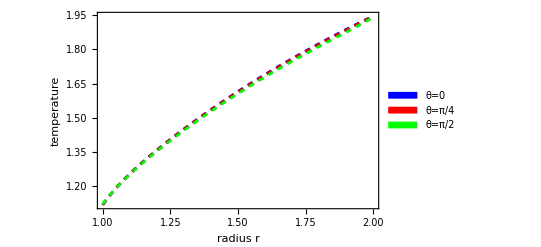

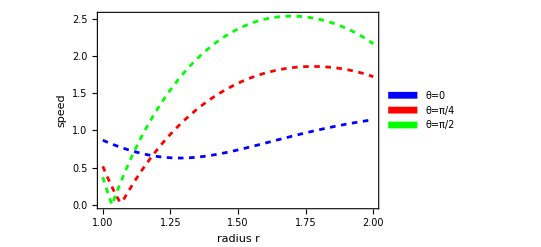

```mathematica
Show[PlotExactTemperature]
Show[PlotExactVelocity]
```

## 3D Plotting

```mathematica
GraphicsRow[{
 Plot3D[temperatureC[x, y], {x, -2.1, 2.1}, {y, -2.1, 2.1}, 
 PlotPoints -> 30, 
 ColorFunction -> Function[{x, y, z}, ColorData["SouthwestColors"][z]], 
 RegionFunction -> Function[{x, y, z}, R0 < Sqrt[x^2 + y^2] < R1], 
 PlotRange -> All,PlotLabel->theory <> " temperature"],
 Plot3D[ux[x, y], {x, -2.1, 2.1}, {y, -2.1, 2.1}, 
 PlotPoints -> 30, 
 ColorFunction -> Function[{x, y, z}, ColorData["SouthwestColors"][z]], 
 RegionFunction -> Function[{x, y, z}, R0 < Sqrt[x^2 + y^2] < R1], 
 PlotRange -> All,PlotLabel->theory <> " x-velocity"],
 Plot3D[uy[x, y], {x, -2.1, 2.1}, {y, -2.1, 2.1}, 
 PlotPoints -> 30, 
 ColorFunction -> Function[{x, y, z}, ColorData["SouthwestColors"][z]], 
 RegionFunction -> Function[{x, y, z}, R0 < Sqrt[x^2 + y^2] < R1], 
 PlotRange -> All,PlotLabel->theory <> " y-velocity"]}]
```

-Graphics-

```mathematica
ToCppFunction[expr_,funcName_:"f",varName_:"r"]:=Module[{code},(*Step 1:CForm the whole expression at once*)code=ToString[CForm[expr]];
(*Step 2:Fast string replacements-no regex where avoidable*)code=StringReplace[code,{(*Bessel functions*)"BesselI(0,"->"cyl_bessel_i(0,","BesselI(1,"->"cyl_bessel_i(1,","BesselK(0,"->"cyl_bessel_k(0,","BesselK(1,"->"cyl_bessel_k(1,",(*If you want to catch any integer order generically:*)RegularExpression["BesselI\\((\\d+),"]:>"cyl_bessel_i($1,",RegularExpression["BesselK\\((\\d+),"]:>"cyl_bessel_k($1,",(*Log and pow*)"Log("->"std::log(","Power("->"std::pow(","Sqrt("->"std::sqrt(","Abs("->"std::abs(","Exp("->"std::exp(",(*Mathematica uses E for Euler's number*)" E "->" M_E "}];
(*Step 3:Assemble*)"// Requires: #include <cmath>\n"<>"// Requires: #include <boost/math/special_functions/bessel.hpp>\n\n"<>"double "<>funcName<>"(double "<>varName<>") {\n"<>"    using boost::math::cyl_bessel_i;\n"<>"    using boost::math::cyl_bessel_k;\n\n"<>"    return "<>code<>";\n"<>"}"]

Print[ToCppFunction[simpleTemp,"f","r"]]
(*Print[ToCppFunction[simplerho,"f","r"]]*)
Print[ToCppFunction[simplep,"f","r"]]
Print[ToCppFunction[simpleux,"f","r"]]
Print[ToCppFunction[simpleuy,"f","r"]]
```

// Requires: #include <cmath>
// Requires: #include <boost/math/special_functions/bessel.hpp>

double f(double r) {
    using boost::math::cyl_bessel_i;
    using boost::math::cyl_bessel_k;

    return 1.1475416669755338 - 1.4136499460087132e-19/std::pow(r,5) - 1.9855291553960966e-18/std::pow(r,4) - 8.503184547098384e-18/std::pow(r,3) - 7.51454581320324e-16/std::pow(r,2) - 0.006824199418861071/r + 0.009607734992218002*r + 1.1347378340243468e-9*std::pow(r,2) - 2.861003252615381e-7*std::pow(r,3) + 7.835105240179381e-8*std::pow(r,4) - 3.2050302992908996e-6*std::pow(r,5) + 2.1335502466342462e-17*cyl_bessel_i(0,18.250101513540354*r) - 2.3955884082321502e-17*cyl_bessel_i(1,18.250101513540354*r) - 7.515152743849166e6*cyl_bessel_k(0,18.250101513540354*r) - 1.7297773670560922e6*cyl_bessel_k(1,18.250101513540354*r) + 1.1304068783278136*std::log(r);
}

// Requires: #include <cmath>
// Requires: #include <boost/math/special_functions/bessel.hpp>

double f(double r) {
    using boost::math::cyl_bessel_i;
    using boost::math::cyl_bessel_k;

    return 0.0018993199772926886 + 2.196493140489761e-19/std::pow(r,5) - 1.820618508617261e-17/std::pow(r,4) + 1.7806835163503867e-16/std::pow(r,3) + 1.4497382343428474e-15/std::pow(r,2) - 0.6945985178625124/r - 0.2277552405043594*r + 2.2637072826466894e-9*std::pow(r,2) - 2.033833348503882e-7*std::pow(r,3) + 8.411870914721436e-7*std::pow(r,4) - 6.155955617129015e-6*std::pow(r,5) + 1.7810877458902648e-17*cyl_bessel_i(0,18.250101513540354*r) - 1.999837203192199e-17*cyl_bessel_i(1,18.250101513540354*r) - 6.273649510565284e6*cyl_bessel_k(0,18.250101513540354*r) - 1.4440181460184255e6*cyl_bessel_k(1,18.250101513540354*r) - 2.0537662284439946e-12*std::log(r);
}

// Requires: #include <cmath>
// Requires: #include <boost/math/special_functions/bessel.hpp>

double f(double r) {
    using boost::math::cyl_bessel_i;
    using boost::math::cyl_bessel_k;

    return -2.0447636553038926 + 1.0359201653139577e-19/std::pow(r,5) + 2.0767426137201643e-18/std::pow(r,4) + 3.1555921783409397e-16/std::pow(r,3) + 2.608427543187341/std::pow(r,2) - 2.270488285671194e-6/r + 3.4283192024707477e-12*r - 0.5693881120084758*std::pow(r,2) - 2.135570368091424e-9*std::pow(r,3) - 1.0672365177466179e-7*std::pow(r,4) + 4.480857814008834e-6*std::pow(r,5) - 2.8359656347824803e-14*cyl_bessel_i(0,14.920428347746274*r) + 2.8359656347824803e-14*cyl_bessel_i(2,14.920428347746274*r) - 388304.5478035767*cyl_bessel_k(0,14.920428347746274*r) + 388304.5478035762*cyl_bessel_k(2,14.920428347746274*r) + 6.945985178621474*std::log(r);
}

// Requires: #include <cmath>
// Requires: #include <boost/math/special_functions/bessel.hpp>

double f(double r) {
    using boost::math::cyl_bessel_i;
    using boost::math::cyl_bessel_k;

    return -9.029638580084187e-12 - 4.7257426603090694e-20/std::pow(r,5) + 1.2549535982543759e-18/std::pow(r,4) - 1.3310760046952658e-16/std::pow(r,3) + 4.908584471553888e-15/std::pow(r,2) + 1.1114114849250902/r - 0.2592858292136669*r + 8.46678012321097e-11*std::pow(r,2) + 6.313585336147986e-9*std::pow(r,3) - 3.827994226840259e-8*std::pow(r,4) + 2.8097142147287375e-7*std::pow(r,5) - 7.033822365876907e-15*cyl_bessel_i(1,14.920428347746274*r) + 155945.4280877491*cyl_bessel_k(1,14.920428347746274*r) - 1.7470036479589143e-12*std::log(r);
}